# METODE NUMERIČNEGA MODELIRANJA

## - Priprave za vaje -

AVTOR: Gašper Bizjan, 23170101, 3. letnik FSLJ

## Priprave za vajo 1

- resevanje problemov upogiba nosilcev (staticno doloceni in staticno nedoloceni problemi)
- uporaba in razumevanje enacbe upogibnice (in dolocitev funkcije povesa - upogibnice)
- osnove Mathematice in poznavanje funkcij: Solve, DSolve, Plot, /. (prepis vrednosti)

## 1. Naloga

Obravnava statično določenega problema upogiba nosilca 1.

### 1. Del

```mathematica
q = 1 (*N/mm*);
L = 2*10^3(*mm*);
Ej = 200 *10^3(*N/mm*);
Iu=177*10^4(*mm^4*);
h=80(*mm*);
```

Velikost reakcij v podporah.

```mathematica
Clear[Ay,By]
r1=Solve[{Ay+By-q*L==0,By*L-q*L^2/2==0}, {Ay,By}];
Ay=Ay/.r1[[1]]
By=By/.r1[[1]]
```

1000

1000

### 2. Del

Izračun in izris notranjega momenta M(x).

1/2 (2000 x-x^2)

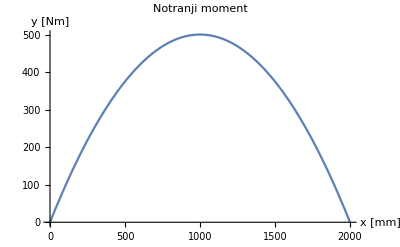

```mathematica
Clear[Mz]
r2=Solve[Mz-Ay*x+q*x^2/2==0,Mz];
Mz[x_]=Mz/.r2[[1]]
Plot[Mz[x]/1000,{x,0,L},PlotLabel->"Notranji moment",AxesLabel->{"x [mm]","y [Nm]"} ]
```

### 3. Del

Določitev in izris upogibnice.

{(8000000000 x-4000 x^3+x^4)/8496000000000}

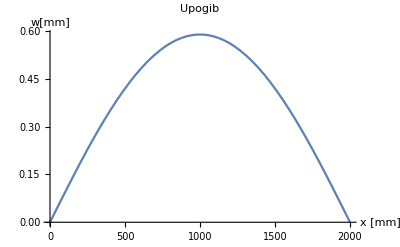

```mathematica
Clear[w]
r31=DSolve[{w''[x]==-Mz[x]/(Ej*Iu),w[0]==0,w[L]==0},w[x],x];
w[x_]=w[x]/.r31
Plot[w[x],{x,0,L}, AxesLabel->{"x [mm]", "w[mm]"},PlotLabel -> "Upogib"]
```

Še z neposredno integracijo.

{x/1062-x^3/2124000000+x^4/8496000000000}

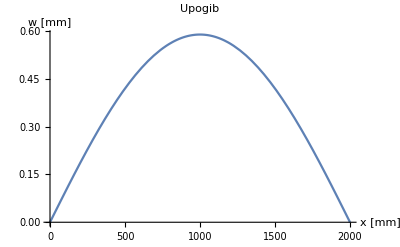

```mathematica
Clear[w,C1,C2]
w''[x_]=-Mz[x]/(Ej*Iu);
w'[x_]=Integrate[w''[x],x]+C1;
w[x_]=Integrate[w'[x],x]+C2;
r32=Solve[{w[0]==0, w[L]==0},{C1,C2}];
w[x_]=w[x]/.r32
Plot[w[x],{x,0,L}, AxesLabel->{"x [mm]", "w [mm]"}, PlotLabel -> "Upogib"]
```

### 4. Del

Določitev in izris upogibnih napetost.

```mathematica
sig[x_,z_]=Mz[x]/Iu*z;
Manipulate[Plot[sig[x,z],{x,0,L},AxesLabel->{"x [mm]", "σ [MPa]"},PlotLabel -> "Upogibna napetost"],{z,-h/2,h/2}]
```

## 2. Naloga

Statično nedoločen nosilec. 

Določitev reakcij in izris notranjega momenta ter povesa.

```mathematica
q = 1 (*N/mm*);
L = 2*10^3(*mm*);
Ej = 200 *10^3(*N/mm*);
Iu=177*10^4(*mm^4*);
```

```mathematica
Clear[Ay,By,Mz,Ma,w, C1, C2]
(*eno enačbo dobimo iz rešitve upogibnice, kjer je Mz(x) notranji moment.*)
Mz[x_]=Ay*x-q*x^2/2-Ma;
w''[x_]=-Mz[x]/(Ej*Iu);
w'[x_]=Integrate[w''[x], x]+C1;
w[x_]=Integrate[w'[x],x]+C2;
(*druge enačbe dobimo iz .*)
r4=Solve[{
Ay+By-q*L==0, 
Ma+By*L-q*L^2/2==0 , 
w[0]==0, w[L]==0, w'[0]==0
},{Ay,By,Ma,C1,C2}]

Mz[x_]=Mz[x]/.r4[[1]]
w[x_]=w[x]/.r4[[1]]
```

{{Ay→1250,By→750,Ma→500000,C1→0,C2→0}}

-500000+1250 x-x^2/2

x^2/1416000-x^3/1699200000+x^4/8496000000000

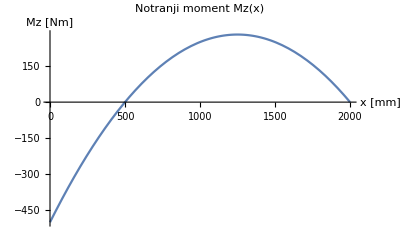

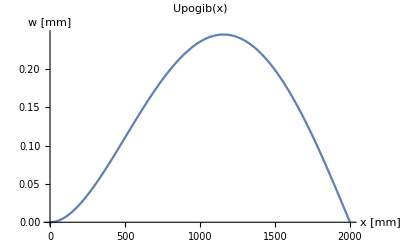

```mathematica
Plot[Mz[x]/1000,{x,0,L}, PlotLabel -> "Notranji moment Mz(x)", AxesLabel->{"x [mm]","Mz [Nm]"}]
Plot[w[x],{x,0,L}, PlotLabel -> "Upogib(x)", AxesLabel->{"x [mm]","w [mm]"}]
```

## 3. Naloga

O uporabi simetrije pri obravnavi problemov upogiba nosilca.

```mathematica
Clear[A,B,Mb]
r=Solve[{A-F/2-q L==0, Mb-A L+q L^2/2==0}, {A, Mb}]
A=A/.r[[1]];
B=A;

Mz[x_]=A x
DSolve[{w''[x]==-Mz[x]/(Ej Iu),w[0]==0,w'[L]==0}, w[x], x]
```

{{A→1/2 (F+2 L q),Mb→1/2 (F L+L^2 q)}}

1/2 (F+2 L q) x

{{w[x]→(3 F L^2 x+6 L^3 q x-F x^3-2 L q x^3)/(12 Ej Iu)}}

## Priprave za vajo 2

- resevanje gibalnih (dinamskih) problemov
- izpeljava in razumevanje gibalnih enacb
- Mathematica: numericno resevanje diferencialnih enacb, funkcije: NDSolve, ParametricPlot, WhenEvent

## 1. Naloga

Obravnava gibanja kroglice.

### 1. Del

Izpeljava enačb.

```mathematica
(*podatki*)
v0=20.;(*m/s*)
α=40°;
H=1.;(*m*)
g=9.81;(*m/s^2*)
m=0.5;(*kg*)
```

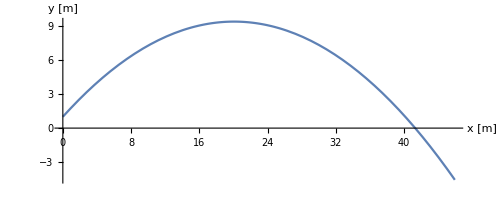

```mathematica
Clear[x,y]
s=NDSolve[{
m x''[t]==0,y''[t]==-g,
x[0]==0, x'[0]==v0 Cos[α],
y[0]==H, y'[0]==v0 Sin[α]
},{x,y},{t,20}];
{x[t_],y[t_]}={x[t],y[t]}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,3}, AxesLabel->{"x [m]","y [m]"}]
```

```mathematica
FindRoot[y[t], {t,0,3}]
x[t]/.%
```

{t→2.69655}

41.3136

### 2. Del

Modeliranje odboja.

```mathematica
(*podatki*)
v0=20.;(*m/s*)
α=40°;
H=1.;(*m*)
g=9.81;(*m/s^2*)
m=0.5;(*kg*)
```

2.69655  s   41.3136  m

5.1915  s   79.5383  m

7.43695  s   113.941  m

9.45785  s   144.903  m

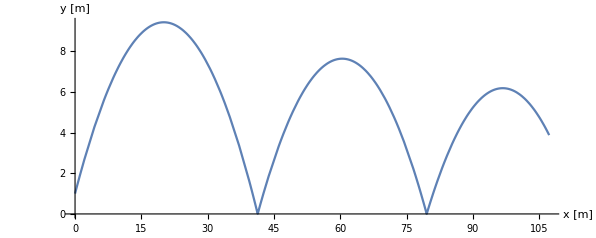

```mathematica
Clear[x,y]
s=NDSolve[{x''[t]==0,y''[t]==-g,
x[0]==0,x'[0]==v0 Cos[α],
y[0]==H, y'[0]==v0 Sin[α],
WhenEvent[y[t]==0, {y'[t]-> -0.9 y'[t], Print[t" s   ",x[t]" m"]}]
},{x,y},{t,10}];

{x[t_],y[t_]}={x[t],y[t]}/.s[[1]];

ParametricPlot[{x[t],y[t]},{t,0,7}, AxesLabel->{"x [m]","y [m]"}]
```

### 3. Del

Upor zraka.

```mathematica
(*podatki*)
v0=20.;(*m/s*)
α=40°;
H=1.;(*m*)
g=9.81;(*m/s^2*)
m=0.5;(*kg*)
β=0.1;(*kg/m*)
```

1.89595  s   12.6115  m

3.13319  s   15.5507  m

4.07907  s   17.0747  m

4.84938  s   18.0594  m

5.49692  s   18.7669  m

6.05164  s   19.3078  m

6.53276  s   19.7383  m

6.95364  s   20.0907  m

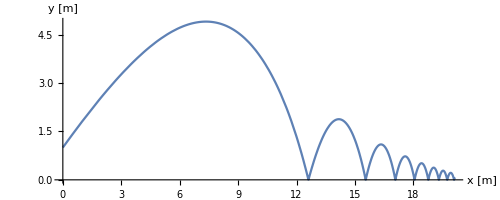

```mathematica
Clear[x,y]
s=NDSolve[{
v=√(x'[t]^2+y'[t]^2);
x''[t]==-β v  x'[t],y''[t]==-g-β v y'[t],
x[0]==0,x'[0]==v0 Cos[α],
y[0]==H, y'[0]==v0 Sin[α],
WhenEvent[y[t]==0, {y'[t]-> -0.9 y'[t], Print[t" s   ",x[t]" m"]}]
},{x,y},{t,7}];

{x[t_],y[t_]}={x[t],y[t]}/.s[[1]];

ParametricPlot[{x[t],y[t]},{t,0,7}, AxesLabel->{"x [m]","y [m]"}]
```

## 2. Naloga

Obravnava gibaja mase na vzmeti.

```mathematica
g = 9.81 (*m/s^2*);
Lz=1.(*cm*);
k=10.(*N/cm*);
m=0.3(*kg*);
```

```mathematica
Clear[x]
s=NDSolve[{
m x''[t]==m g - k(x[t]-Lz),
x[0]==Lz, x'[0]==0
},x,{t,0,5}];

x[t_]=x[t]/.s[[1]];

Animate[Plot[-x[t],{t,0,t1},PlotRange->{{0,t1},{-2,0}},AxesLabel->{"t [s]","x [cm]"}],{t1,0,5}]
```

```mathematica
Animate[ListLinePlot[{{0,0},{0,-x[tk]}},
PlotRange ->{{-0.1,0.1},{-2,0}},
Mesh -> All,
PlotStyle-> Directive[Black, Thick],
MeshStyle-> Directive[PointSize[0.03], Black],
Axes-> {False,True}],
{tk,0.01,5}]
```

## 3. Naloga

Obravnava gibanja dveh mas na vzmeteh.

```mathematica
(*parametri*)
g=9.81(*m/s^2*);
{m1,m2}={0.3,0.2}(*kg*);
{k1,k2}={20,15}(*N/cm*);
{L1,L2}={1.0,1.0}(*cm*);
```

```mathematica
Clear[x1,x2]
s=NDSolve[{
m1 x1''[t]==m1 g-k1(x1[t]-L1)+k2(x2[t]-x1[t]-L2),
m2 x2''[t]==m2 g-k2(x2[t]-x1[t]-L2),
x1[0]==L1, x2[0]==x1[0]+L2,
x1'[0]==x2'[0]==0
},{x1,x2},{t,10}];
{x1[t_],x2[t_]}={x1[t], x2[t]}/.s[[1]];
Animate[
Show[
ListLinePlot[{{0,0},{0,-x1[tk]}}, 
PlotRange->{{-0.1,0.1},{-3,0}},
Mesh -> All,
PlotStyle-> Directive[Black, Thick],
MeshStyle-> Directive[PointSize[0.03], Black],
Axes-> {False,False}],
ListLinePlot[{{0,-x1[tk]},{0,-x2[tk]}}, 
PlotRange->{{-0.1,0.1},{-4,0}},
Mesh -> All,
PlotStyle-> Directive[Red, Thick],
MeshStyle-> Directive[PointSize[0.03], Black],
Axes-> {False,False}]
]
,{tk,0.01,5}]
```

## 4. Naloga

Obravnava gibanja matematičnega nihala.

```mathematica
g=9.81(*m/s^2*);
m=0.5(*kg*);
L=1.0(*m*);
```

```mathematica
Clear[ϕ,Fv]
s1=NDSolve[{
r=L;
r ϕ''[t]==-g Sin[ϕ[t]],
ϕ[0]==π/3, ϕ'[0]==0
},ϕ,{t,10}];
ϕ[t_]=ϕ[t]/.s1[[1]];

s2=Solve[-m r ϕ'[t]^2==-Fv[t]+m g Cos[ϕ[t]],Fv[t]];
Fv[t_]=Fv[t]/.s2[[1]];
```

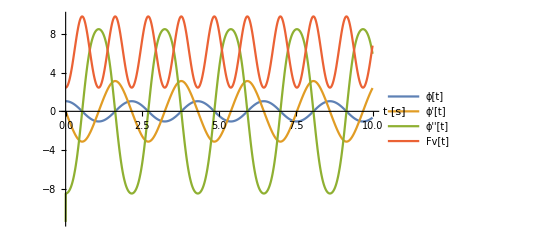

```mathematica
Plot[{ϕ[t],ϕ'[t],ϕ''[t],Fv[t]},{t,0,10}, AxesLabel->{"t [s]",None},PlotLegends->{"ϕ[t]","ϕ'[t]","ϕ''[t]","Fv[t]"}]
```

```mathematica
Animate[
Row[{Show[
ParametricPlot[{r Sin[ϕ[t]],-r Cos[ϕ[t]]},{t,0,tk},PlotRange->{{-1,1},{-1.1,0}},
PlotStyle->Directive[Black, Thin, Dashed], Axes->{True,False}],
ListLinePlot[{{0,0},{r Sin[ϕ[tk]], -r Cos[ϕ[tk]]}}, Mesh->All,
MeshStyle->Directive[PointSize[0.03], Black]],
ImageSize-> Medium
],

Show[
Plot[m g Cos[ϕ[t]]+m r ϕ'[t]^2, {t,0,tk}, PlotRange->{{0,5},{-1,10}},
PlotStyle->Directive[Red, Thin], PlotLegends->{"Fv[t]"}],
ImageSize -> Medium
]}],
{tk,0.01,5}]
```

## 5. Naloga

Obravnava gibanja podajnega nihala.

```mathematica
g=9.81(*m/s^2*);
m=0.2(*kg*);
L=1.0(*m*);
k=30.(*N/m*);
```

```mathematica
Clear[ϕ,r]
s=NDSolve[{
m(r''[t]-r[t] ϕ'[t]^2)==m g Cos[ϕ[t]]-k(r[t]-L),
r[t] ϕ''[t]+2 r'[t]ϕ'[t]==-g Sin[ϕ[t]],
r[0]==L+0.1, r'[0]==0,
ϕ[0]==π/3,ϕ'[0]==0
},{r,ϕ},{t,0,10}];
ϕ[t_]=ϕ[t]/.s[[1]];
r[t_]=r[t]/.s[[1]];

Animate[
Show[
ParametricPlot[{r[t] Sin[ϕ[t]],-r[t] Cos[ϕ[t]]},{t,0,tk}, PlotRange->{{-1,1},{0,-2}}, PlotStyle->Directive[Black,Thin,Dashed], Axes->{True,False}],
ListLinePlot[{{0,0},{r[tk] Sin[ϕ[tk]], -r[tk] Cos[ϕ[tk]]}},Mesh->All,MeshStyle->Directive[PointSize[0.03], Black]],
ImageSize-> Medium
],
{tk,0.01,5}]
```

## Priprave za vajo 3

- resevanje (obravnava) enoosnih problemov (z enim in z vec polji)
- razumevanje vodilne enacbe problema, dolocitve robnih pogojev in pogojev prehoda
- Mathematica: resevanje problemov z resevanjem diferencialne enacbe ali pa z uporabo nastavka za resitev. Uporaba funkcij: DSolve, Solve

## 1. Naloga

Reševanje enoosnih problemov

### 1. in 2. Del

Vodilna enačba problema, določitev robnih pogojev, pristop reševanja (i), rešitev v Mathematici.

```mathematica
(*parametri*)
n0=2.(*N/mm*);
A=200.(*mm^2*);
Ej=200000.(*N/mm^2*);
L=2000 (*mm*);
F=1000.(*N*);
```

```mathematica
Clear[u]
s=DSolve[{
Ej A u''[x]==-n0,
u[0]==0,
Ej A u'[L]==F
},u[x],x];
u[x_]=u[x]/.s[[1]]
```

0.000125 x-2.5×10^-8 x^2

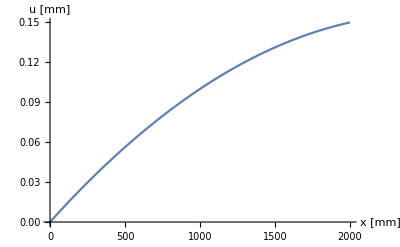

```mathematica
Plot[{u[x]},{x,0,L}, AxesLabel->{"x [mm]","u [mm]"}]
```

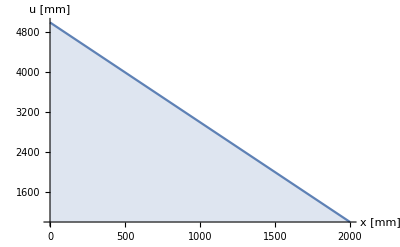

```mathematica
Ns[x_]=Ej A u'[x];
Plot[{Ns[x]},{x,0,L}, AxesLabel->{"x [mm]","u [mm]"}, Filling->Bottom]
```

pristop reševanja (ii)

```mathematica
Clear[un, C1, C2]
un[x_]=-n0/(Ej A) x^2/2+C1 x + C2;
r=Solve[{un[0]==0, Ej A un'[L]==F},{ C1, C2}];
un[x_]=un[x]/.r[[1]];
Plot[{un[x]},{x,0,L}, AxesLabel->{"x [mm]","u [mm]"}]
```

-Graphics-

```mathematica
Ns2[x_]=Ej A u'[x];
Plot[{Ns2[x]},{x,0,L}, AxesLabel->{"x [mm]","u [mm]"}, Filling->Bottom]
```

-Graphics-

## 2. Naloga

Reševanje enoosnih problemov z upoštevanjem temperaturne spremembe. Določi u(x), N(x) in σ(x).

```mathematica
(*parametri*)
A=200.(*mm^2*);
Ej=200000.(*N/mm^2*);
L=2000 (*mm*);
ΔT0=50.(*oC*);
α=1.2 10^-5(*mm/oC*);
k=10000.(*N/mm*);
```

-0.4+0.0005 x-1.5×10^-7 x^2

50.-0.025 x

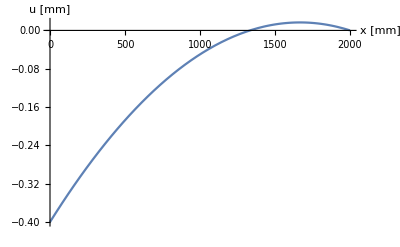

```mathematica
Clear[u]
s=DSolve[{
ΔT[x_]=ΔT0-x/L ΔT0;
u''[x]-α ΔT'[x]==0,
u[L]==0, 
Ej A (u'[0]-α ΔT[0])==k u[0]
},u[x],x];
u[x_]=u[x]/.s[[1]]
ΔT[x_]=ΔT[x]/.s[[1]]

Plot[{u[x]},{x,0,L}, AxesLabel->{"x [mm]","u [mm]"}]
```

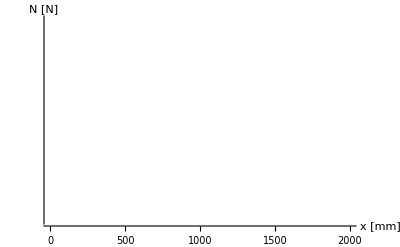

```mathematica
Ns[x_]=Ej A (u'[x]-α ΔT[x]);
Plot[{Ns[x]},{x,0,L}, AxesLabel->{"x [mm]","N [N]"}, Filling->Axis]
```

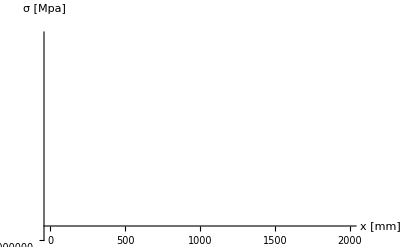

```mathematica
σu[x_]=Ns[x]/A;
Plot[{σu[x]},{x,0,L}, AxesLabel->{"x [mm]","σ [Mpa]"}, Filling->Axis]
```

## 3. Naloga

Reševanje enoosnih problemov z več polji. Določi u(x), N(x).

```mathematica
(*parametri*)
{n1,n2}={2.,1.}(*N/mm*);
{A1,A2}={500.,200.}(*mm^2*);
Ej=200000.(*N/mm^2*);
L=2000. (*mm*);
F=1000.(*N*);
```

```mathematica
Clear[u1,u2]
s=DSolve[{
Ej A1 u1''[x]==-n1,Ej A2 u2''[x]==-n2,
u1[0]==0,u2[2 L]==0,
u1[L]==u2[L],Ej A1 u1'[L]-Ej A2 u2'[L]==F
},{u1[x],u2[x]},x];
{u1[x_],u2[x_]}={u1[x],u2[x]}/.s[[1]]
```

{0.0000485714 x-1.×10^-8 x^2,0.0142857+0.0000464286 x-1.25×10^-8 x^2}

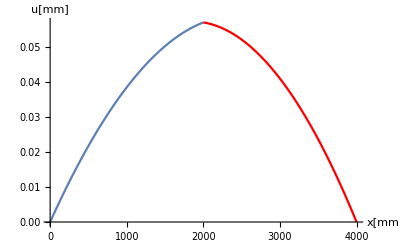

```mathematica
Show[Plot[u1[x],{x,0,L},AxesLabel->{"x[mm]","u[mm]"}],
Plot[u2[x],{x,L,2L},AxesLabel->{"x[mm]","u[mm]"},PlotStyle->Red],
PlotRange->All]
```

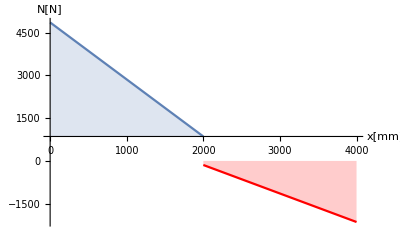

```mathematica
Ns1[x_]=Ej A1 u1'[x];
Ns2[x_]=Ej A2 u2'[x];
Show[Plot[Ns1[x],{x,0,L},AxesLabel->{"x[mm]","N[N]"},Filling->Axis],
Plot[Ns2[x],{x,L,2L},AxesLabel->{"x[mm]","N[N]"},PlotStyle->Red,Filling->Axis],
PlotRange->All]
```

## 4. Naloga

Reševanje enoosnih problemov: obravnava spreminjajoče porazdeljene obremenitve n(x). Določi u(x), N(x).

```mathematica
(*parametri*)
n0=2.(*N/mm*);
A=200.(*mm^2*);
Ej=200000.(*N/mm^2*);
L=2000. (*mm*);
k=10000.(*N*);
```

```mathematica
Clear[u]
s=DSolve[{
n[x_]=2 n0-x/L n0;
Ej A u''[x]==-n[x],
u[0]==0,
Ej A u'[L]==-k u[L]
},u[x],x];
u[x_]=u[x]/.s[[1]]
```

0.000127778 x-5.×10^-8 x^2+4.16667×10^-12 x^3

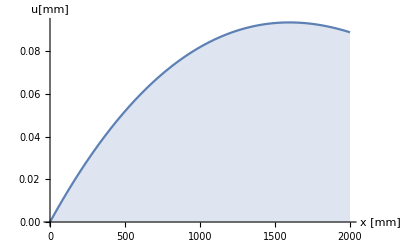

```mathematica
Plot[u[x],{x,0,L}, AxesLabel->{"x [mm]","u[mm]"}, Filling->Axis]
```

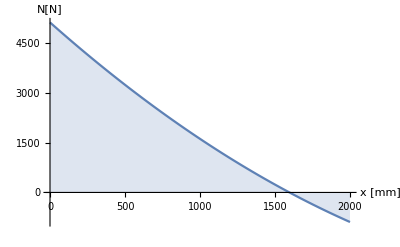

```mathematica
Ns[x_]=Ej A u'[x];
Plot[Ns[x],{x,0,L}, AxesLabel->{"x [mm]","N[N]"}, Filling->Axis]
```

## 5. Naloga

u(x), N(x), σ(x)

```mathematica
(*parametri*)
L = 2000.(*mm*);
n0 = 2(*N/mm*);
F = 1000(*N*);
Ej = 200000(*MPa*);
A1 = 200(*mm*);
A2 = 100(*mm*);
```

```mathematica
n[x_] = n0/(2 L) x;
Clear[u1,u2]
r = DSolve[{
Ej A1 u1''[x] == +n[x],
u2''[x] == 0,
u1[0] == 0,
-F == Ej A2 u2'[3 L],
u1[2L] == u2[2L],
Ej A1 u1'[2L] == Ej A2 u2'[2L]
},{u1,u2},x];
{u1[x_], u2[x_]} = {u1[x], u2[x]}/.r[[1]]
```

{-0.000125 x+2.08333×10^-12 x^3,-0.166667-0.00005 x}

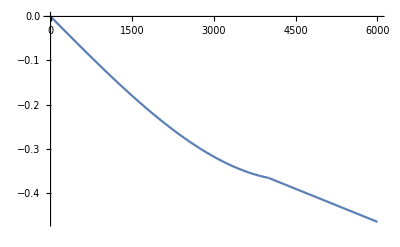

```mathematica
p1 = Plot[u1[x], {x,0,2L}];
p2 = Plot[u2[x], {x,2L, 3 L}];
Show[{p1, p2}, PlotRange -> All]
```

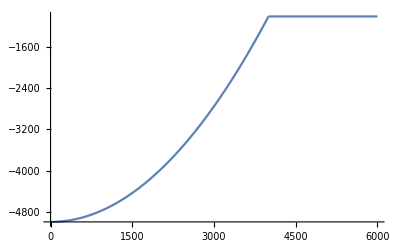

```mathematica
N1[x_] = Ej A1 u1'[x];
N2[x_] = Ej A2 u2'[x];
pp1 = Plot[N1[x], {x,0,2L}];
pp2 = Plot[N2[x], {x,2L, 3L}];
Show[{pp1, pp2}, PlotRange -> All]
```

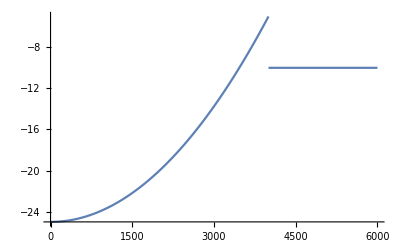

```mathematica
σ1[x_] = N1[x]/A1;
σ2[x_] = N2[x]/A2;
ppp1 = Plot[σ1[x], {x,0,2L}];
ppp2 = Plot[σ2[x], {x,2L, 3L}];
Show[{ppp1, ppp2}, PlotRange -> All]
```

## 6. Naloga

```mathematica
(*parametri*)
L=2000.;
n0=2.;
F=1000.;
Ej=200000.;
A=100.;
A1=200.;
A2=100.;
```

```mathematica
Clear[u1,u2]
n[x_]=x/L n0;
s=DSolve[{
Ej A1 u1''[x]==-n[x],u2''[x]==0,
u1[0]==0,
Ej A2 u2'[3 L]==-F,
u1[L]==u2[L],
Ej A1 u1'[L]==Ej A2 u2'[L]
},{u1[x],u2[x]},x];
u1[x_]=u1[x]/.s[[1]];
u2[x_]=u2[x]/.s[[1]];
```

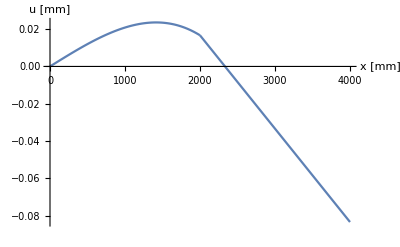

```mathematica
Show[{
Plot[u1[x],{x,0,L}],
Plot[u2[x],{x,L,2L}]
},PlotRange->All,AxesLabel->{"x [mm]","u [mm]"}]
```

## 7. Naloga

Narejena v zvezku

## 8. Naloga

```mathematica
(*Parametri*)
L=2000.(*mm*);
A=100.(*mm^2*);
A1=A;
A2=2 A;
n0=2.(*N/mm*);
F=1000. (*N*);
Ej=200000(*N/mm^2*);
k=1000(*N/mm*);
dT0=40(*oC*);
α=1.2 10^-5(*K^-1*);
```

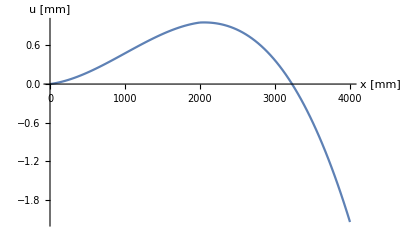

```mathematica
Clear[u1,u2]
s=DSolve[{
dT[x_]=x (x-L) (-4 dT0)/L^2;
Ej A1 (u1''[x]-α dT'[x])==0, Ej A2 (u2''[x]-α dT'[x])==0,
u1[0]==0,
Ej A2 (u2'[2L]-α dT[2L])==-k u2[2L],
u1[L]==u2[L],
-Ej A1 (u1'[L]-α dT[L])+Ej A2 (u2'[L]-α dT[L])==-F
},{u1[x],u2[x]},x];
u1[x_]=u1[x]/.s[[1]];
u2[x_]=u2[x]/.s[[1]];

p1=Plot[u1[x],{x,0,L}];
p2=Plot[u2[x],{x,L,2L}];
Show[{p1,p2},PlotRange-> All, AxesLabel-> {"x [mm]","u [mm]"}]
```

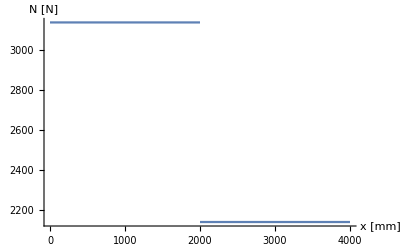

```mathematica
N1[x_]=Ej A1 (u1'[x]-α dT[x]);
N2[x_]=Ej A2(u2'[x]-α dT[x]);
p11=Plot[N1[x],{x,0,L}];
p22=Plot[N2[x],{x,L,2L}];
Show[{p11,p22},PlotRange-> All, AxesLabel-> {"x [mm]","N [N]"}]
```

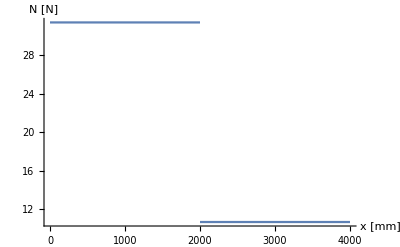

```mathematica
σ1[x_]=N1[x]/A1;
σ2[x_]=N2[x]/A2;
p11=Plot[σ1[x],{x,0,L}];
p22=Plot[σ2[x],{x,L,2L}];
Show[{p11,p22},PlotRange-> All, AxesLabel-> {"x [mm]","N [N]"}]
```

## Priprave za vajo 4

- aproksimativno funkcijsko reševanje enoosnih primerov
- razumevanje ekzaktnega in aproksimativnega reševanja robnega problema
- določitev minimalne stopnje polinoma za aproksimativno rešitev
- reševanje v Mathematici

## 1. Naloga

Uvod v aproksimativno reševanje.

```mathematica
g=9.81(*m/s^2*);
L=1.(*m*);

Clear[ϕ]
NDSolve[{
ϕ''[t] L==-g Sin[ϕ[t]],
ϕ[0]==π/3, ϕ'[0]==0
},ϕ[t],{t,0,10}];
ϕ[t_]=ϕ[t]/.%;
```

```mathematica
Manipulate[Plot[{ϕ[t],a Cos[t b]},{t,0,5}],{a,1,2},{b,1,3}]
```

## 2. Naloga

Načini eksaktnega in aproksimativnega reševanjana na enoosnem primeru.

### 1. Del

Načini eksaktnega reševanja

#### a) direktno reševanje DE

```mathematica
n[x_]=n0(1-x/L);
Clear[u]
s=DSolve[{Ej A u''[x]==-n[x],u[L]==0,Ej A u'[0]==0},u[x],x];
u[x_]=u[x]/.s[[1]]
```

(16000000000-6000 x^2+x^3)/240000000000

```mathematica
(*Preverimo rešitev*)
Ej A u''[x] (*leva = desna*);
FullSimplify[Ej A u''[x]]
```

n0 (-1+x/L)

#### b) Integracija

```mathematica
Clear[u]
u''[x_]=-n0/(Ej A)(1-x/L)
u'[x_]=Integrate[u''[x],x]+C0
u[x_]=Integrate[u'[x],x]+C1
```

-(n0 (1-x/L))/(A Ej)

C0+(n0 (-L x+x^2/2))/(A Ej L)

C1+C0 x-(n0 x^2)/(2 A Ej)+(n0 x^3)/(6 A Ej L)

```mathematica
Clear[C0,C1]
s=Solve[{u[L]==0,Ej A u'[0]==0},{C0,C1}]
{C0,C1}={C0,C1}/.s[[1]];
```

{{C0→0,C1→(L^2 n0)/(3 A Ej)}}

```mathematica
u[x]
```

(L^2 n0)/(3 A Ej)-(n0 x^2)/(2 A Ej)+(n0 x^3)/(6 A Ej L)

```mathematica
(*Preverimo rešitev*)
Ej A u''[x] (*leva = desna*)
FullSimplify[%]
```

A Ej (-n0/(A Ej)+(n0 x)/(A Ej L))

n0 (-1+x/L)

#### c) Nastavek splošne rešitve

```mathematica
Clear[C0,C1,C2,C3]
u[x_]=C0+C1 x+C2 x^2+C3 x^3;
n[x_]=n0(1-x/L);

s=Solve[{
u[L]==0,
Ej A u'[0]==0,
Ej A u''[0]==-n[0],
Ej A u''[L]==-n[L]
},{C0,C1,C2,C3}]
{C0,C1,C2,C3}={C0,C1,C2,C3}/.s[[1]];
```

{{C0→(L^2 n0)/(3 A Ej),C1→0,C2→-n0/(2 A Ej),C3→n0/(6 A Ej L)}}

```mathematica
u[x]
```

(L^2 n0)/(3 A Ej)-(n0 x^2)/(2 A Ej)+(n0 x^3)/(6 A Ej L)

```mathematica
(*Preverimo rešitev*)
FullSimplify[Ej A u''[x]]
```

n0 (-1+x/L)

### 2. Del

Načini aproksimativnega reševanja

```mathematica
Clear[C0,C1,C2]
ua[x_]=C0+C1 x +C2 x^2;
n[x_]=n0(1-x/L);
Solve[{
ua[L]==0, 
Ej A ua'[0]==0, 
Ej A ua''[L/2]==-n0(1-L/(2L))
},{C0,C1,C2}]
{C0,C1,C2}={C0,C1,C2}/.%[[1]];
```

{{C0→1/20,C1→0,C2→-1/80000000}}

```mathematica
ua[x]
```

1/20-x^2/80000000

```mathematica
(*preverimo rešitev*)
Ej A ua''[x]
```

-1

### Primerjava 1. in 2. Dela

```mathematica
Ej=200000(*MPa*);
A=200(*mm^2*);
n0=2(*N/mm*);
L=2000(*mm*);
```

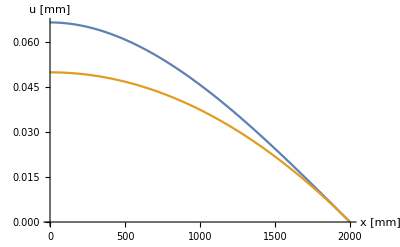

```mathematica
Plot[{u[x],ua[x]},{x,0,L},AxesLabel->{"x [mm]","u [mm]"}]
```

## 3. Naloga

Določitev aproksimativne (funkcijske) rešitve u(x) enoosnega problema, pri čemer je u(x) polinom drugega reda.

```mathematica
n0=2.;(*N/mm*)
L=2000.;(*mm*)
A=200.;(*mm^2*)
Ej=200000.;(*MPa*)
```

```mathematica
(*Najprej dobimo ekzaktno rešitev.*)
Clear[u]
s=DSolve[{n[x_]=n0 Sin[π/L x];Ej A u''[x]==-n[x],u[0]==0,u'[L]==0},u[x],x]
u[x_]=u[x]/.s[[1]];
```

{{u[x]→0.000031831 x+0.0202642 Sin[0.0015708 x]}}

```mathematica
(*Aproksimativna rešitev 2. reda.*)
Clear[c0,c1,c2]
s1=NSolve[
u1[x_]=c0+c1 x + c2 x^2;
n[x_]=n0 Sin[π/L x];{
u1[0]==0, u1'[L]==0, Ej A u1''[L/2]==-n[L/2]
},{c0,c1,c2}]
u1[x_]=u1[x]/.s1[[1]];
```

{{c0→0.,c1→0.0001,c2→-2.5×10^-8}}

```mathematica
u1[x]
```

0.+0.0001 x-2.5×10^-8 x^2

### a) Izboljšava z uporabo polinoma višje stopnje

```mathematica
(*Aproksimativna rešitev 2. reda.*)
Clear[c0,c1,c2,c3]
s2=NSolve[
u2[x_]=c0+c1 x + c2 x^2+c3 x^3;
n[x_]=n0 Sin[π/L x];{
u2[0]==0, u2'[L]==0, Ej A u2''[L/3]==-n[L/3],Ej A u2''[2L/3]==-n[2L/3]
},{c0,c1,c2,c3}]
u2[x_]=u2[x]/.s2[[1]];
```

{{c0→0.,c1→0.0000866025,c2→-2.16506×10^-8,c3→-1.38778×10^-27}}

```mathematica
u2[x]
```

0.+0.0000866025 x-2.16506×10^-8 x^2-1.38778×10^-27 x^3

```mathematica
Plot[{u[x],u1[x],u2[x]},{x,0,L},AxesLabel->{"x [mm]","u [mm]"},PlotLabels-> {"Eksaktna","Aproksimativna - polinom 2. reda","Aproksimativna - polinom 3. reda"}]
```

-Graphics-

### b) Izboljšava z delitvijo domene

```mathematica
n[x_]=n0 Sin[π/L x];
u21[x_]=c0+c1 x + c2 x^2;
u22[x_]=d0+d1 x + d2 x^2;

Clear[c0,c1,c2,d0,d1,d2]
s3=NSolve[{
u21[0]==0,u22[0]==0,
u21[L/2]==u22[L/2],
u21'[L/2]==u22'[L/2],
Ej A u21''[L/4]==-n[L/4],
Ej A u22''[3L/4]==-n[3L/4]
},{c0,c1,c2,d0,d1,d2}]
u21[x_]=u21[x]/.s3[[1]];
u22[x_]=u21[x]/.s3[[1]];
```

{{c0→0.,c1→0.+1. d1,c2→-1.76777×10^-8,d0→0.,d2→-1.76777×10^-8}}

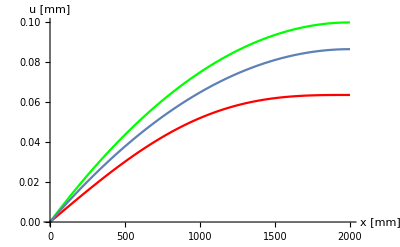

```mathematica
p0=Plot[u[x],{x,0,L},PlotStyle-> Red];
p1=Plot[u1[x],{x,0,L},PlotStyle-> Green];
p2=Plot[u2[x],{x,0,L}];
p21=Plot[u21[x],{x,0,L/2}];
p22=Plot[u22[x],{x,L/2,L}];
Show[{p0,p1,p2,p21,p22},AxesLabel->{"x [mm]","u [mm]"},PlotRange-> All]
```

## 4. Naloga

Določi funkcijo pomika u(x) palice. Obravnavaj prvič ekzaktno in nato aproksimativno na različne načine.

```mathematica
L=2000.;(*mm*)
h=50.;(*mm*)
a0=200.;(*mm*)
a1=100.;(*mm*)
dT0=30.;(*K*)
α=1.2 10^-5;(*mmK/mm*)
Ej=200000;(*MPa*)
```

```mathematica
A[x_]=h (a0+(a1-a0)/L x);
dT[x_]=dT0(1-x/L);
```

Hitro ugotovimo, da ekzaktne rešitve ni.

### Aproksimativno numerično (NDSolve)

```mathematica
Clear[u]
s=NDSolve[{
Ej A'[x] (u'[x]-α dT[x])+Ej A[x] (u''[x]-α dT'[x])==0,
u[0]==0, u[L]==0
},u[x],{x,0,L}]
u[x_]=u[x]/.s[[1]];
```

{{u[x]→InterpolatingFunction[…][x]}}

### Aproksimativno funkcijsko

#### a) S polinomom 2. reda

```mathematica
ua[x_]=c0+c1 x + c2 x^2;
DE[x_]=D[Ej A[x] (ua'[x]-α dT[x]),x];
Clear[c0,c1,c2]
sa=NSolve[{
ua[0]==0,
ua[L]==0,
DE[L/2]==0
},{c0,c1,c2}]
ua[x_]=ua[x]/.sa[[1]]
```

{{c0→0.,c1→0.00024,c2→-1.2×10^-7}}

0.+0.00024 x-1.2×10^-7 x^2

#### b) S polinomom 3. reda

```mathematica
ub[x_]=c0+c1 x + c2 x^2+c3 x^3;
DE[x_]=D[Ej A[x] (ub'[x]-α dT[x]),x];
Clear[c0,c1,c2,c3]
sb=NSolve[{
ub[0]==0,
ub[L]==0,
DE[L/3]==0,
DE[2L/3]==0
},{c0,c1,c2,c3}];
ub[x_]=ub[x]/.sb[[1]]
```

0.+0.000226667 x-1.×10^-7 x^2-6.66667×10^-12 x^3

#### c) Z dvema podintervaloma domene in s polinomom 2. stopnje

```mathematica
uc1[x_]=c0+c1 x+c2 x^2;
uc2[x_]=d0+d1 x+d2 x^2;
DE1[x_]=D[Ej A[x] (uc1'[x]-α dT[x]),x];
DE2[x_]=D[Ej A[x] (uc2'[x]-α dT[x]),x];
Clear[c0,c1,c2,d0,d1,d2]
sc=NSolve[{
uc1[0]==0,
uc2[L]==0,
uc1[L/2]==uc2[L/2],
uc1'[L/2]==uc2'[L/2],
DE1[L/4]==0,
DE2[3L/4]==0
},{c0,c1,c2,d0,d1,d2}];
uc1[x_]=uc1[x]/.sc[[1]]
uc2[x_]=uc2[x]/.sc[[1]]
```

0.+0.000232941 x-1.11176×10^-7 x^2

-0.0211765+0.000275294 x-1.32353×10^-7 x^2

### Grafični prikaz

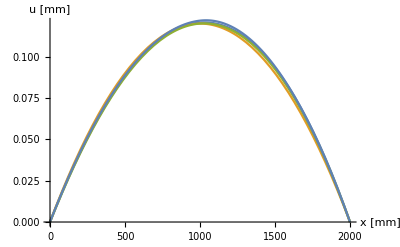

-Graphics-

```mathematica
Show[{
Plot[{u[x],ua[x],ub[x]},{x,0,L}],
Plot[uc1[x],{x,0,L/2}],
Plot[uc2[x],{x,L/2,L}]
},AxesLabel->{"x [mm]","u [mm]"}]

Show[{
Plot[{u[x],ua[x],ub[x]},{x,0,L},PlotRange->{{950,1050},{0.118,0.122}},PlotLabels-> {"Num.","(a)","(b)"}],
Plot[uc1[x],{x,0,L/2},PlotStyle->Green,PlotRange->{{950,1050},{0.118,0.122}}],
Plot[uc2[x],{x,L/2,L},PlotStyle->Green,PlotLabels->"(c)",PlotRange->{{950,1050},{0.118,0.122}}]
},AxesLabel->{"x [mm]","u [mm]"}]
```

## 5. Naloga

```mathematica
(*Parametri*)
L=2000.(*mm*);
n0=2.(*N/mm*);
F=1000.(*N*);
Ej=200000.(*MPa*);
A=200.(*mm^2*);
```

```mathematica
n[x_]=n0 Sin[x/L π];
u1[x_]=c0+c1 x+c2 x^2+c3 x^3;
u2[x_]=d0+d1 x+d2 x^2+d3 x^3;

s=NSolve[{
u1[0]==0, Ej A u2'[L]==-F,
u1[L/2]==u2[L/2],u1'[L/2]==u2'[L/2],
Ej A u1''[L/6]==-n[L/6],Ej A u1''[2L/6]==-n[2L/6],
Ej A u2''[4L/6]==-n[4L/6],Ej A u2''[5L/6]==-n[5L/6]
},{c0,c1,c2,c3,d0,d1,d2,d3}];
{u1[x_],u2[x_]}={u1[x],u2[x]}/.s[[1]]
```

{0.+0.0000433013 x-3.34936×10^-9 x^2-9.15064×10^-12 x^3,-0.0183013+0.0000982051 x-5.82532×10^-8 x^2+9.15064×10^-12 x^3}

```mathematica
N1[x_]=Ej A u1'[x]
N2[x_]=Ej A u2'[x]
```

4.×10^7 (0.0000433013-6.69873×10^-9 x-2.74519×10^-11 x^2)

4.×10^7 (0.0000982051-1.16506×10^-7 x+2.74519×10^-11 x^2)

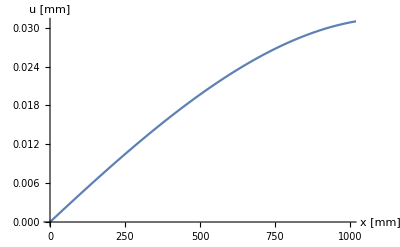

```mathematica
Show[{
Plot[u1[x],{x,0,L/2}],
Plot[u2[x],{x,L/2,L}]
},AxesLabel-> {"x [mm]","u [mm]"}]
```

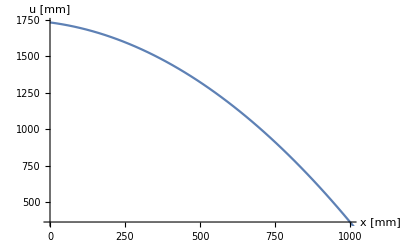

```mathematica
Show[{
Plot[N1[x],{x,0,L/2}],
Plot[N2[x],{x,L/2,L}]
},AxesLabel-> {"x [mm]","u [mm]"}]
```

## 6. Naloga

```mathematica
(*Parametri*)
L=2000.(*mm*);
n0=5.(*N/mm*);
F=1000.(*N*);
Ej=200000.(*MPa*);
a0=50.(*mm*);
Δa=30.(*mm*);
h=40.(*mm*);

A[x_]=h (a0-Δa/L x);
```

```mathematica
DE1[x_]=D[Ej A[x]u1'[x],x];
DE2[x_]=D[Ej A[x]u2'[x],x];
u1[x_]=c0+c1 x+c2 x^2+c3 x^3;
u2[x_]=d0+d1 x+d2 x^2+d3 x^3;

Clear[c0,c1,c2,c3,d0,d1,d2,d3]
s=NSolve[{
u1[0]==0, Ej A[L] u2'[L]==F,
u1[L/2]==u2[L/2],u1'[L/2]==u2'[L/2],
DE1[L/6]==-n0,DE1[2L/6]==-n0,
DE2[4L/6]==-n0,DE2[5L/6]==-n0
},{c0,c1,c2,c3,d0,d1,d2,d3}];
{u1[x_],u2[x_]}={u1[x],u2[x]}/.s[[1]]
```

{0.+0.0000269933 x-1.98451×10^-9 x^2-7.2164×10^-13 x^3,0.00276373+0.0000195313 x+4.64844×10^-9 x^2-2.65625×10^-12 x^3}

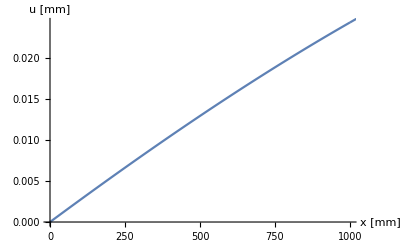

```mathematica
Show[{
Plot[{u1[x]},{x,0,L/2}],
Plot[u2[x],{x,L/2,L}]
},AxesLabel-> {"x [mm]","u [mm]"}]
```

```mathematica
N1[x_]=Ej A[x] u1'[x]
N2[x_]=Ej A[x] u2'[x]
```

8.×10^6 (50.-0.015 x) (0.0000269933-3.96902×10^-9 x-2.16492×10^-12 x^2)

8.×10^6 (50.-0.015 x) (0.0000195313+9.29687×10^-9 x-7.96875×10^-12 x^2)

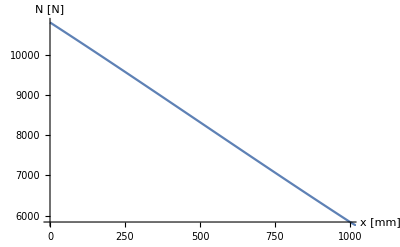

```mathematica
Show[{
Plot[{N1[x]},{x,0,L/2}],
Plot[N2[x],{x,L/2,L}]
},AxesLabel-> {"x [mm]","N [N]"}]
```

## 7. Naloga

```mathematica
(*Parametri*)
L=2000.(*mm*);
n0=2.(*N/mm*);
F=1000.(*N*);
Ej=200000.(*MPa*);
A=200.(*mm^2*);
```

```mathematica
Clear[c0,c1,c2,c3]
n[x_]=n0 Cos[(x π)/(2 L)];
u[x_]=c0+c1 x +c2 x^2+c3 x^3;
s=NSolve[{
u[0]==0,
u'[L]==F,
Ej A u''[L/3]==-n[L/3] ,
Ej A u''[2L/3]==-n[2L/3]
},{c0,c1,c2,c3}];
u[x_]=u[x]/.s[[1]]
```

0.+1000. x-3.08013×10^-8 x^2+4.57532×10^-12 x^3

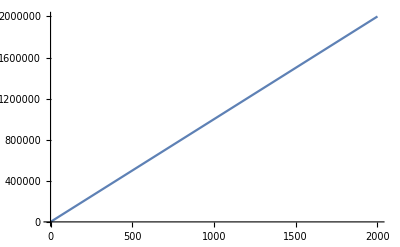

```mathematica
Plot[u[x],{x,0,L}]
```

## Priprave za vajo 5

- resevanje (obravnava) enoosnih problemov po metodi koncnih razlik (MKR)
- zapis enacb robnega problema (enoosni primeri) v diferencni obliki
- Mathematica: delo z matrikami, izris vektorja tock, resevanje matricnega sistema enacb.

## 1. Naloga

### 1. Del

Snovanje matrik in dostopanje do posameznih členov matrike.

```mathematica
M={
{1,2,1,0,0,0},
{0,1,2,1,0,0},
{0,0,1,2,1,0},
{0,0,0,1,2,1}
};
MatrixForm[M]
```

(1 | 2 | 1 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 1 | 2 | 1)

```mathematica
M[[3]]
```

{0,0,1,2,1,0}

```mathematica
M[[2,3]]=5
MatrixForm[M]
```

5

(1 | 2 | 1 | 0 | 0 | 0
0 | 1 | 5 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 1 | 2 | 1)

```mathematica
M[[2,2;;4]]
M[[2,{2,3,4}]]
```

{1,5,1}

{1,5,1}

```mathematica
M[[2,{3,1,5}]]={7,8,9}
MatrixForm[M]
```

{7,8,9}

(1 | 2 | 1 | 0 | 0 | 0
8 | 1 | 7 | 1 | 9 | 0
0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 1 | 2 | 1)

```mathematica
M=({{1, 2, 1, 0, 0, 0}, {0, 1, 2, 1, 0, 0}, {0, 0, 1, 2, 1, 0}, {0, 0, 0, 1, 2, 1}})(*insert -> Matrix*)
```

{{1,2,1,0,0,0},{0,1,2,1,0,0},{0,0,1,2,1,0},{0,0,0,1,2,1}}

### 2. Del

Uporaba funkcije Table in For zanke.

```mathematica
M=Table[0,{i,4},{j,6}] (*Matrika ničel*)
M//MatrixForm
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
For[i=1,i≤ 4,i++,M[[i,{i,i+1,i+2}]]={1,2,1};Print[M[[i]]]]
```

{1,2,1,0,0,0}

{0,1,2,1,0,0}

{0,0,1,2,1,0}

{0,0,0,1,2,1}

### 3. del

Izris vektorja točk, ListPlot.

{{0.,10},{0.5,11},{1.,12},{1.5,12},{2.,10.5},{2.5,12},{3.,14}}

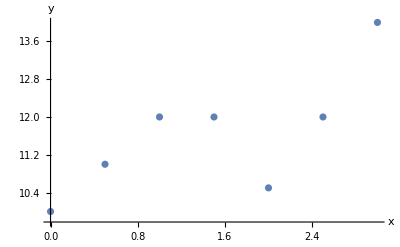

```mathematica
y={10,11,12,12,10.5,12,14};
xy=Table[{(i-1) 0.5,y[[i]]},{i,Length[y]}]
ListPlot[xy,AxesLabel->{"x","y"}]
```

## 2. Naloga

Problem obravnavaj po metodi končnih razlik (MKR). Korak mreže naj bo h = L/5

```mathematica
n0 = 2.(*N/mm*);
L=2000. (*mm*);
F=1000. (*N*);
A=200.(*mm^2*);
Ej = 200. 10^3(*MPa*);
```

### 1. Del

Določitev enačb problema in zapis enačb v diferenčni obliki.

### 2. Del

Zapis sistema enačb v matrični obliki in reševanje.

#### a) Enostavni način

```mathematica
h=L/5;
M=({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 1}, {1, -2, 1, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0}, {0, 0, 0, 0, 0, 1, -2, 1}});
b=({{0}, {2 h F/(Ej A)}, {-n0 h^2/(Ej A)}, {-n0 h^2/(Ej A)}, {-n0 h^2/(Ej A)}, {-n0 h^2/(Ej A)}, {-n0 h^2/(Ej A)}, {-n0 h^2/(Ej A)}});
U=LinearSolve[M,b]
```

{{-0.054},{0.},{0.046},{0.084},{0.114},{0.136},{0.15},{0.156}}

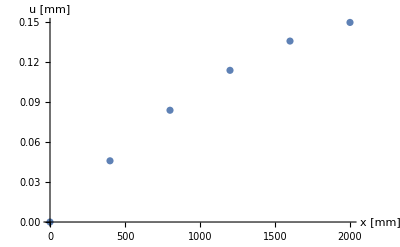

```mathematica
ListPlot[Table[{(i-1)h,U[[i+1,1]]},{i,1,6}],AxesLabel->{"x [mm]","u [mm]"}]
```

#### b) naprednejši način

```mathematica
del = 5;
h=L/del;
n=del+3;

(*Matrika koeficientov M in vektor rezultatov b*)
M=Table[0,{i,1,n},{j,1,n}];
M[[1,2]]=1;
M[[2,{-3,-1}]]={-1,1};

b=Table[0,{i,1,n}];
b[[2]]=2 h F/(Ej A);
b[[2]]=2 h F/(Ej A);

For[i=1,i≤n-2,i++,
 M[[i+2,{i,i+1,i+2}]]={1,-2,1};
b[[i+2]]=-n0 h^2/(Ej A);
]
(*izračun neznanega pomika*)
U=LinearSolve[M,b]

Print[MatrixForm[M],MatrixForm[U],"=",MatrixForm[b]]
ListPlot[Table[{(i-1) h,U[[i+1]]},{i,1,del+1}],AxesLabel->{"x [mm]","u [mm]"}]
```

{-0.054,0.,0.046,0.084,0.114,0.136,0.15,0.156}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(-0.054
0.
0.046
0.084
0.114
0.136
0.15
0.156)=(0
0.02
-0.008
-0.008
-0.008
-0.008
-0.008
-0.008)

-Graphics-

### 3. Del

Določitev notranje osne sile v palici po MKR.

True

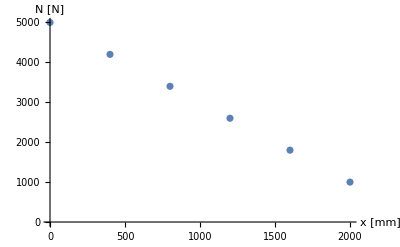

```mathematica
Ni1=Table[0,{i,1,n-2}];
For[i=1,i≤ n-2,i++,
Ni1[[i]]=Ej A (U[[i+2]]-U[[i]])/(2 h);
]

Ni2 = Table[Ej A (U[[i+2]]-U[[i]])/(2 h),{i,1,n-2}];

Ni1==Ni2

ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}], AxesLabel->{"x [mm]","N [N]"}]
```

## 3. Naloga

Reševanje enoosnega primera po MKR. Izračunaj pomik in napetosti.

```mathematica
n0 = 3.(*N/mm*);
n1 = 2.(*N/mm*);
L=2000. (*mm*);
F=1000. (*N*);
A=200.(*mm^2*);
Ej = 200. 10^3(*MPa*);

nx[x_]=n0+(n1-n0)/L x(*N/mm*);
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(-0.066
0.
0.054
0.0968
0.1292
0.152
0.166
0.172)=(0
0.02
-0.012
-0.0112
-0.0104
-0.0096
-0.0088
-0.008)

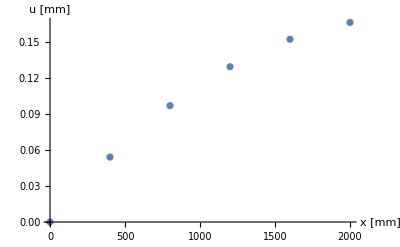

```mathematica
del = 5.;
h=L/del;
n=del+3;

(*definirajmo M, b*)

M=Table[0,{i,1,n},{j,1,n}];
M[[1,2]]=1;
M[[2,{-3,-1}]]={-1,1};

b=Table[0,{i,1,n}];
b[[2]]=F 2h/(Ej A);

For[i=1,i≤ n-2,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1};
b[[i+2]]=-nx[h (i-1)] h^2/(Ej A);
]
(*Prikaz matričnega izračuna in grafa pomika*)
U=LinearSolve[M,b];
Print[MatrixForm[M],MatrixForm[U],"=",MatrixForm[b]]
ListPlot[Table[{(i-1)h,U[[i+1]]},{i,1,n-2}],AxesLabel->{"x [mm]","u [mm]"}]
```

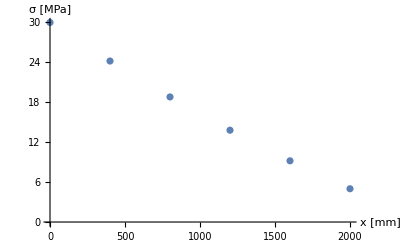

```mathematica
σ=Table[Ej (U[[i+2]]-U[[i]])/(2h),{i,1,n-2}];
ListPlot[Table[{(i-1)h,σ[[i]]},{i,1,n-2}],AxesLabel->{"x [mm]","σ [MPa]"}]
```

## 4. Naloga

Določitev enačb problema in zapis v diferenčni obliki, MKR pomik in napetosti.

```mathematica
L=2000. (*mm*);
h1=50.;(*mm*);
a0=200. (*mm*);
a1=100. (*mm*);
Ej = 200. 10^3(*MPa*);
dT0=30.(*0C*);
α=1.2 10^-5(*/K*);

A[x_]=h1 (a0+(a1-a0)/L x);
dT[x_]=dT0(1-x/L);
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1.0125 | -2. | 0.9875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.9875 | -1.95 | 0.9625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.9625 | -1.9 | 0.9375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.9375 | -1.85 | 0.9125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.9125 | -1.8 | 0.8875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.8875 | -1.75 | 0.8625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.8625 | -1.7 | 0.8375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.8375 | -1.65 | 0.8125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.8125 | -1.6 | 0.7875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7875 | -1.55 | 0.7625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7625 | -1.5 | 0.7375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7375 | -1.45 | 0.7125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7125 | -1.4 | 0.6875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6875 | -1.35 | 0.6625 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6625 | -1.3 | 0.6375 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6375 | -1.25 | 0.6125 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6125 | -1.2 | 0.5875 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5875 | -1.15 | 0.5625 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5625 | -1.1 | 0.5375 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5375 | -1.05 | 0.5125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5125 | -1. | 0.4875)(-0.0240746
0.
0.0219499
0.0417583
0.0594068
0.0748759
0.0881441
0.0991882
0.107983
0.1145
0.118711
0.12058
0.120072
0.117147
0.111759
0.103857
0.0933877
0.0802865
0.0644832
0.0458975
0.024438
0.
-0.0275374)=(0
0
-0.0027
-0.00261
-0.00252
-0.00243
-0.00234
-0.00225
-0.00216
-0.00207
-0.00198
-0.00189
-0.0018
-0.00171
-0.00162
-0.00153
-0.00144
-0.00135
-0.00126
-0.00117
-0.00108
-0.00099
-0.0009)

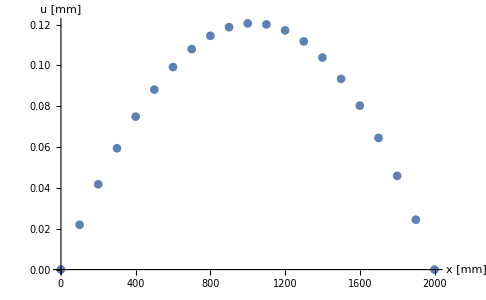

```mathematica
(*Število polj za MKR*)
d=20;
h=L/d;
n=d+3;
(*Definirajmo matriko K in vektor b*)
K=Table[0,{i,1,n},{j,1,n}];
K[[1,2]]=1;
K[[2,-2]]=1;

b=Table[0,{i,1,n}];

For[i=1,i≤ n-2,i++,
K[[i+2,{i,i+1,i+2}]]=A'[(i-1)h]/(2h){-1,0,1}+A[(i-1)h]/h^2{1,-2,1};
b[[i+2]]= α(A'[x_]dT[(i-1)h]+A[(i-1)h] dT'[(i-1)h]);
]

U=LinearSolve[K,b];
Print[MatrixForm[K],MatrixForm[U],"=",MatrixForm[b]]
ListPlot[Table[{(i-1)h,U[[i+1]]},{i,1,n-2}],AxesLabel->{"x [mm]","u [mm]"}]
```

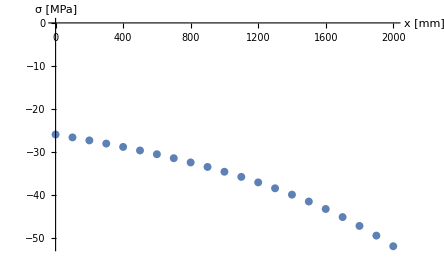

```mathematica
σ=Table[Ej((U[[i+2]]-U[[i]])/(2h)-α dT[(i-1)h]),{i,1,n-2}];
ListPlot[Table[{(i-1)h,σ[[i]]},{i,1,n-2}],AxesLabel->{"x [mm]","σ [MPa]"}]
```

## 5. Naloga

Prikazani osno obremenjeni element obravnavaj po MKR.

```mathematica
L=2000.(*mm*);
n0=2.(*N/mm*);
k=5000.(*N/mm*);
Ej=200000.(*MPa*);
A=200.(*mm^2*);
F=1000.(*N*);
nx[x_]=n0 Cos[x/2 L π];
```

### Za definirano št. polj

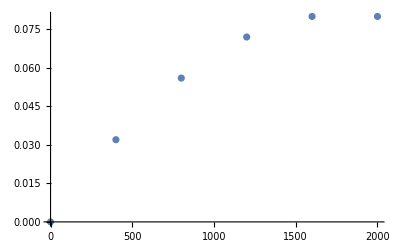

```mathematica
h=L/5;
n=8;
M=({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -Ej A, 2 h k, Ej A}, {1, -2, 1, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0}, {0, 0, 0, 0, 0, 1, -2, 1}});
b=({{0}, {0}, {-nx[0] h^2/(Ej A)}, {-nx[h] h^2/(Ej A)}, {-nx[2h] h^2/(Ej A)}, {-nx[3h] h^2/(Ej A)}, {-nx[4h] h^2/(Ej A)}, {-nx[5h] h^2/(Ej A)}});
U=LinearSolve[M,b];
U=Flatten[U];

ListPlot[Table[{(i-1)h,U[[i+1]]},{i,1,n-2}]]
```

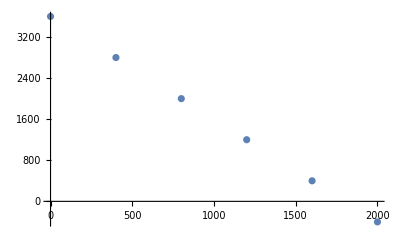

```mathematica
Ni=Table[Ej A (U[[i+1]]-U[[i-1]])/(2h),{i,2,n-1}];
ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}]]
```

### Poljubno polj

```mathematica
d=5;
h=L/5;
n=d+3;

M=Table[0,{i,1,n},{j,1,n}];
M[[1,2]]=1;
M[[2,{-3,-2,-1}]]={-Ej A, 2 k h, Ej A};

b=Table[0,{i,1,n}];

For[i=1,i≤n-2,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1};
b[[i+2]]=-nx[(i-1)h]h^2/(Ej A);
]

U=LinearSolve[M,b];
U=Flatten[U];

Print[MatrixForm[M],MatrixForm[U],"=",MatrixForm[b]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -4.×10^7 | 4.×10^6 | 4.×10^7
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(-0.04
0.
0.032
0.056
0.072
0.08
0.08
0.072)=(0
0
-0.008
-0.008
-0.008
-0.008
-0.008
-0.008)

```mathematica
ListPlot[Table[{(i-1)h,U[[i+1]]},{i,1,n-2}]]
```

-Graphics-

```mathematica
Ni=Table[Ej A (U[[i+1]]-U[[i-1]])/(2h),{i,2,n-1}];
ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}]]
```

-Graphics-

## 6. Naloga

Prikazani osno obremenjeni element obravnavaj po MKR.

```mathematica
L=2000.(*mm*);
n0=2.(*N/mm*);
k=5000.(*N/mm*);
Ej=200000.(*MPa*);
A=200.(*mm^2*);
F=1000.(*N*);
dT0=30(*0C*);
α=1.2 10^-5(*/K*);

dT[x_]=dT0(x/L)^3;
```

#### 6.

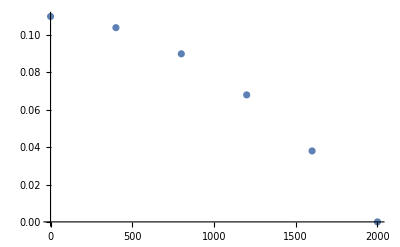

```mathematica
h=L/5;
n=8;
xi[i_]=(i-1)h;
M=({{0, 0, 0, 0, 0, 1, 0, 0}, {-1, 0, 1, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0}, {0, 1, -2, 1, 0, 0, 0, 0}, {0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0}, {0, 0, 0, 0, 1, -2, 1, 0}, {0, 0, 0, 0, 0, 1, -2, 1}});
b=({{0}, {-2h F/(Ej A)}, {h^2/(Ej A) (-n0+α dT'[xi[1]])}, {h^2/(Ej A) (-n0+α dT'[xi[2]])}, {h^2/(Ej A) (-n0+α dT'[xi[3]])}, {h^2/(Ej A) (-n0+α dT'[xi[4]])}, {h^2/(Ej A) (-n0+α dT'[xi[5]])}, {h^2/(Ej A) (-n0+α dT'[xi[6]])}});
U=LinearSolve[M,b];
U=Flatten[U];

ListPlot[Table[{(i-1)h,U[[i]]},{i,1,n-2}]]
```

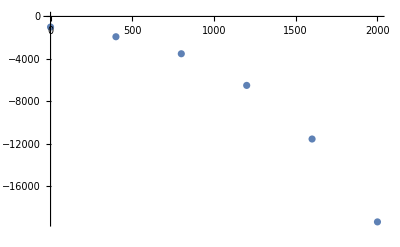

```mathematica
Ni=Table[Ej A ((U[[i+2]]-U[[i]])/(2h)-α dT[(i-1)h]),{i,1,n-2}];
ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}]]
```

#### 8

```mathematica
d=5;
h=L/d;
n=d+3;
xi[i_]=(i-1)h;

M=Table[0,{i,1,n},{j,1,n}];
M[[1,6]]=1;
M[[2,{1,2,3}]]={-1,0,1};

b=Table[0,{i,1,n}];
b[[2]]=-2h F/(Ej A);

For[i=1,i≤ n-2,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1};
b[[i+2]]=h^2/(Ej A) (-n0+α dT'[xi[i]]);
]
U=LinearSolve[M,b];
Print[MatrixForm[M],MatrixForm[U],MatrixForm[b]]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(0.11
0.104
0.09
0.068
0.038
0.
-0.046
-0.1)(0
-0.02
-0.008
-0.008
-0.008
-0.008
-0.008
-0.008)

```mathematica
ListPlot[Table[{(i-1)h,U[[i]]},{i,1,n-2}]]
```

-Graphics-

```mathematica
Ni=Table[Ej A ((U[[i+2]]-U[[i]])/(2h)-α dT[(i-1)h]),{i,1,n-2}];
ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}]]
```

-Graphics-

#### 10

```mathematica
d=5;
h=L/d;
n=d+3;
xi[i_]=(i-1)h;

d=5;
h=L/d;
n=d+3;
xi[i_]=(i-1)h;

M=Table[0,{i,1,n},{j,1,n}];
M[[1,6]]=1;
M[[2,{1,2,3}]]={-Ej A, -2 h k, Ej A};

b=Table[0,{i,1,n}];

For[i=1,i≤ n-2,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1};
b[[i+2]]=h^2/(Ej A) (-n0+α dT'[xi[i]]);
]
U=LinearSolve[M,b];
Print[MatrixForm[M],MatrixForm[U],MatrixForm[b]]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-4.×10^7 | -4.×10^6 | 4.×10^7 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(0.0466666
0.0533333
0.052
0.0426667
0.0253333
0.
-0.0333333
-0.0746666)(0
0
-0.008
-0.008
-0.008
-0.008
-0.008
-0.008)

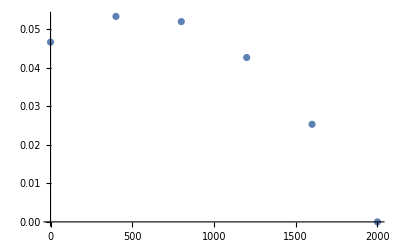

```mathematica
ListPlot[Table[{(i-1)h,U[[i]]},{i,1,n-2}]]
```

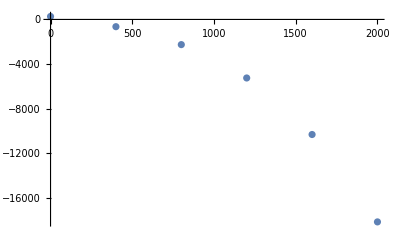

```mathematica
Ni=Table[Ej A ((U[[i+2]]-U[[i]])/(2h)-α dT[(i-1)h]),{i,1,n-2}];
ListPlot[Table[{(i-1)h,Ni[[i]]},{i,1,n-2}]]
```

## Priprave za vajo 6

- resevanje (obravnava) enoosnih problemov po metodi koncnih elementov (MKE) -- eno polje in vec polj
- izpeljava enacbe dvovozliscnega koncnega elementa
- Mathematica: delo z matrikami, izris vektorja tock

## Naloga 1

Obravnavanje problema po MKE.

```mathematica
n0=2.(*N/mm*);
L=1000.(*mm*);
Ej=200 10^3(*MPa*);
A=200.(*mm^2*);
F=1000.(*N*);
```

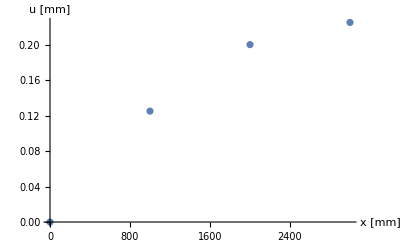

```mathematica
Ke= (Ej A)/L({{1, -1, 0, 0}, {-1, 2, -1, 0}, {0, -1, 2, -1}, {0, 0, -1, 1}});
U=({{0}, {U2}, {U3}, {U4}});
Ff=({{Ra}, {0}, {F}, {F}});
Fn=({{n0 L/2}, {n0 L}, {n0 L/2}, {0}});

s=Solve[Ke.U==Ff+Fn];
{U,Ff}={U,Ff}/.s[[1]];
U=Flatten[U];
Ff=Flatten[Ff];

xi=Range[0,3 L, L];
ListPlot[Table[{xi[[i]],U[[i]]},{i,1,4}],AxesLabel->{"x [mm]","u [mm]"}]
```

## Naloga 2

Problem obravnavaj po MKE. Uporabi 4 dvovozliščne končne elemente.

```mathematica
n0=5(*N/mm*);
L=2000.(*mm*);
Ej =200000. (*MPa*);
A=100.(*mm^2*);
k=10000.(*N/mm*);
α=1.2 10^-5(*/K*);
dT=15(*oC*);
```

### Enostavni način

```mathematica
Le=L/4;
Ke=(Ej A)/Le({{1, -1, 0, 0, 0}, {-1, 2, -1, 0, 0}, {0, -1, 2, -1, 0}, {0, 0, -1, 2, -1}, {0, 0, 0, -1, 1}});
U=({{0}, {U2}, {U3}, {U4}, {U5}});
Ff=({{Ra}, {0}, {0}, {0}, {-k U5}});
Fn=({{n0 Le/2}, {n0 Le}, {n0 Le}, {n0 Le}, {n0 Le/2}});
Ft=Ej A α dT({{-1}, {0}, {0}, {0}, {1}});
s=Solve[Ke.U==Ff+Fn+Ft];
Ur=U/.s[[1]];
Ur=Flatten[Ur]
```

{0,0.20125,0.34,0.41625,0.43}

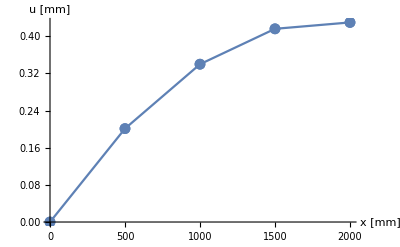

```mathematica
xi=Range[0,L,Le];
ListLinePlot[Table[{xi[[i]],Ur[[i]]},{i,1,5}],AxesLabel->{"x [mm]","u [mm]"},Mesh->Full]
```

### Naprednejši način

```mathematica
ele=4;
n=ele+1;
h=L/ele;
Kel[Ee_,Aa_,Le_]= (Ee Aa)/Le ({{1, -1}, {-1, 1}});

Ke=Table[0,{i,1,n},{j,1,n}];
Ff=Fn=FT=Table[0, {i,1,n}];

For[i=1,i≤ ele, i++,
Ke[[{i,i+1},{i,i+1}]]+=Kel[Ej,A,h];
Fn[[{i,i+1}]]+={n0 h/2,n0 h/2};
FT[[{i,i+1}]]+= Ej A α dT{-1,1}
]

U=Table[Subscript[u, i],{i,1,n}];
U[[1]]=0;

Ff[[1]]=Ra;
Ff[[-1]]=-k U[[-1]]

Print[MatrixForm[Ke],MatrixForm[U],"=",MatrixForm[Ff],MatrixForm[Fn],MatrixForm[FT]]
```

-10000. u_5

(40000. | -40000. | 0 | 0 | 0
-40000. | 80000. | -40000. | 0 | 0
0 | -40000. | 80000. | -40000. | 0
0 | 0 | -40000. | 80000. | -40000.
0 | 0 | 0 | -40000. | 40000.)(0
u_2
u_3
u_4
u_5)=(Ra
0
0
0
-10000. u_5)(1250.
2500.
2500.
2500.
1250.)(-3600.
0.
0.
0.
3600.)

```mathematica
s=Solve[Ke.U==Ff+Fn+FT];
Ur=U/.s[[1]];
Ur=Flatten[Ur]
```

{0,0.20125,0.34,0.41625,0.43}

```mathematica
xi=Range[0,L,h];
ListLinePlot[Table[{xi[[i]],Ur[[i]]},{i,1,n}], Mesh->Full,AxesLabel->{"x [mm]","u [mm]"}]
```

-Graphics-

## Naloga 3

Problem obravnavaj po MKE. Za vsako polje uporabi 3 dvovozliščne končne elemente in reši splošno.

```mathematica
{n1,n2}={4.,2.}(*N/mm*);
{L1,L2}={2000.,1500.}(*mm*);
{A1,A2}={400.,150.}(*mm^2*);
Ej =200000. (*MPa*);
F=1000(*N*);

Kel[Ae_,Le_]= (Ej Ae)/Le({{1, -1}, {-1, 1}});
```

{0,0.0336735,0.0632653,0.0887755,0.110204,0.127551,0.140816,0.15,0.15925,0.167,0.17325,0.178,0.18125,0.183,0.18325,0.182,0.17925,0.175}

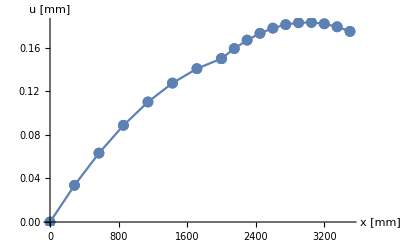

```mathematica
(*Parametri KE*)
ele1=7;
ele2=10;
ele=ele1+ele2;
n=ele+1;
h1=L1/ele1;
h2=L2/ele2;
(*Matrike in vektorji*)
U=Table[Subscript[u, i],{i,1,n}];
Ke=Table[0,{i,1,n},{j,1,n}];
Ff=Fn=Table[0,{i,1,n}];
For[i=1,i≤ ele1,i++,
Ke[[{i,i+1},{i,i+1}]]+=Kel[A1,h1];
Fn[[{i,i+1}]]+={n1 h1/2,n1 h1/2};
]
For[i=1,i≤ ele2,i++,
Ke[[{i+ele1,i+ele1+1},{i+ele1,i+ele1+1}]]+=Kel[A2,h2];
Fn[[{i+ele1,i+ele1+1}]]+={n2 h2/2,n2 h2/2};
]
(*Robni pogoji*)
U[[1]]=0;
Ff[[1]]=Ra;
Ff[[-1]]=-F;
(*Solve*)
s=Solve[Ke.U==Ff+Fn];
Ur=U/.s[[1]];
Ur=Flatten[Ur]
(*Graf*)
xi1=Range[0,L1,h1];
xi2=Range[0,L2,h2];
p1=ListLinePlot[Table[{xi1[[i]],Ur[[i]]},{i,1,ele1+1}], Mesh->Full];
p2=ListLinePlot[Table[{xi1[[-1]]+xi2[[i]],Ur[[ele1+i]]},{i,1,ele2+1}], Mesh->Full];
Show[p1,p2,PlotRange-> All,AxesLabel-> {"x [mm]","u [mm]"}]
```

## Naloga 4

Obravnavaj po MKE in določi ter izriši diskretne vrednosti pomika U.

```mathematica
(*Enote: mm, N, MPa, K*)
L=1000 ;
{n1,n2}={2.,5.};
{A1,A2}={200.,600.};
Ej=200000.;
F=1000.;
dT0=30.;
α=1.2 10^-5;
```

{{Rb→-7000.,u_1→-0.6575,u_2→-0.5865,u_3→-0.5175,u_4→-0.4505,u_5→-0.3855,u_6→-0.3225,u_7→-0.288375,u_8→-0.254667,u_9→-0.221375,u_10→-0.1885,u_11→-0.156042,u_12→-0.124,u_13→-0.092375,u_14→-0.0611667,u_15→-0.030375}}

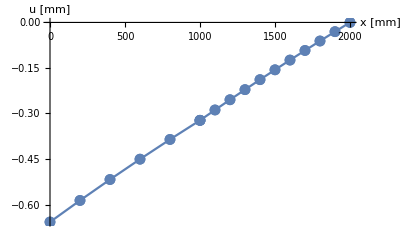

```mathematica
(*parametri KE*)
ele1=5;
ele2=10;
n=ele1+ele2+1;
h1=L/ele1;
h2=L/ele2;
Kel[Ae_,Le_]= (Ej Ae)/Le ({{1, -1}, {-1, 1}});
(*Matrike, vektorji*)
Ke=Table[0,{i,1,n},{i,1,n}];
Ff=Fn=FT=Table[0,{i,1,n}];
For[i=1,i≤ ele1,i++,
Ke[[{i,i+1},{i,i+1}]]+=Kel[A1,h1];
Fn[[{i,i+1}]]+={n1 h1/2,n1 h1/2};
FT[[{i,i+1}]]+=Ej A1 α dT0{-1,1}
]
For[i=1,i≤ ele2,i++,
Ke[[{ele1+i,ele1+i+1},{ele1+i,ele1+i+1}]]+=Kel[A2,h2];
Fn[[{ele1+i,ele1+i+1}]]+={n2 h2/2,n2 h2/2};
FT[[{i+ele1,i+1+ele1}]]+=Ej A2 α dT0{-1,1}
]
U=Table[Subscript[u, i],{i,1,n}];
(*Robni pogoji*)
U[[-1]]=0;
Ff[[1]]=0;
Ff[[-1]]=Rb;
(*Print[MatrixForm[Ke],MatrixForm[U],"=",MatrixForm[Ff],MatrixForm[Fn],MatrixForm[FT]]*)
(*reševanje*)
s=Solve[Ke.U==Ff+Fn+FT]
Ur=U/.s[[1]];
Ur=Flatten[Ur];
(*Graf*)
xi1=Range[0,L,h1];
xi2=Range[L,2L,h2];
p1=ListLinePlot[Table[{xi1[[i]],Ur[[i]]},{i,1,ele1+1}],Mesh->Full];
p2=ListLinePlot[Table[{xi2[[i]],Ur[[i+ele1]]},{i,1,ele2+1}],Mesh->Full];
Show[p1,p2,PlotRange-> All,AxesLabel-> {"x [mm]","u [mm]"}]
```

## Priprave za vajo 7

- izpeljava enacbe dvovozliscnega koncnega elementa
- obravnava enoosnih primerov po MKE s spremenljivo porazdeljeno obtezbo n(x)
- dolocitev notranje osne sile po MKE

## 1. Naloga

Obravnava primera s spremenljivo obtežbo n(x) po MKE. 
Določiti je potrebno pomike in notranjo osno silo vzdolž palice s štirimi 2-vozliščnimi KE. Reši splošno.

```mathematica
n0=5.(*N/mm*);
Lc=2000.(*mm*);
Ej=200000.(*MPa*);
A=100.(*mm^2*);
F=1000.(*N*);

nx[x_]=n0-n0 x/Lc;

Kel[Ee_,Ae_,Le_]=(Ee Ae)/Le ({{1, -1}, {-1, 1}});
```

```mathematica
(*Parametri KE*)
ele=4;
h=Lc/ele;
n=ele+1;

(*Matrika togosti in vektorji*)
Ke=Table[0,{i,1,n},{i,1,n}];
Ff=Fn=Table[0,{i,1,n}];

For[i=1,i≤ele,i++,
Ke[[{i,i+1},{i,i+1}]]+=Kel[Ej,A,h];
x0=(i-1) h;
Fn1=Integrate[nx[x+x0](1-x/h),{x,0,h}];
Fn2 =Integrate[nx[x+x0](x/h),{x,0,h}];
Fn[[{i,i+1}]]+={Fn1,Fn2};
]

U=Table[Subscript[u, i],{i,1,n}];

(*Robni pogoji*)
U[[1]]=0;
{Ff[[1]],Ff[[-1]]}={Ra,F};

s=Solve[Ke.U==Ff+Fn];
Ur=U/.s[[1]];
Ur=Flatten[Ur];
Print[MatrixForm[Ke],MatrixForm[U],"=",MatrixForm[Ff],MatrixForm[Fn]]
```

(40000. | -40000. | 0 | 0 | 0
-40000. | 80000. | -40000. | 0 | 0
0 | -40000. | 80000. | -40000. | 0
0 | 0 | -40000. | 80000. | -40000.
0 | 0 | 0 | -40000. | 40000.)(0
u_2
u_3
u_4
u_5)=(Ra
0
0
0
1000.)(1145.83
1875.
1250.
625.
104.167)

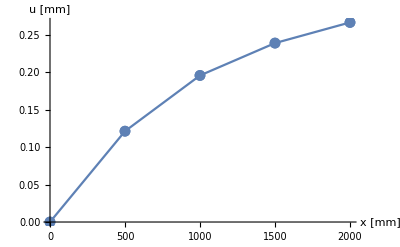

```mathematica
(*Pomik*)
xi=Range[0,Lc,h];
ListLinePlot[Table[{xi[[i]],Ur[[i]]},{i,1,n}],Mesh->Full,AxesLabel->{"x [mm]","u [mm]"}]
```

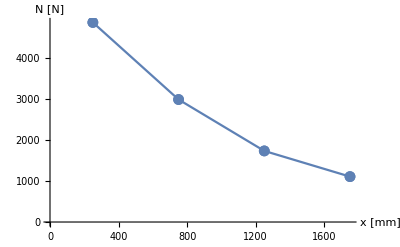

```mathematica
(*Notranja osna sila*)
Ni=Table[0,{i,1,ele}];
For[i=1,i≤ ele,i++,
Ni[[i]]=Ej A/h (-Ur[[i]]+Ur[[i+1]])
]
ListLinePlot[Table[{(i-1)h+h/2,Ni[[i]]},{i,1,ele}],Mesh->Full,AxesLabel->{"x [mm]","N [N]"}]
```

## 2. Naloga

(Naloga #1 v dokumentu)
Prikazani osno obremenjeni element obravnavaj po MKE. Uporabi dvovozliščne KE. Določi ter izriši vozliščne vrednosti pomika ter notranje osne sile.

### Ocena 8

Nalogo reši za poljubno število končnih elementov.

```mathematica
(*enote: mm, N, MPa*)
L=1000.;
n0=5.;
A=100.;
Ej=200000.;
F=1000.;

nx[x_]=n0 (1-0.6 (x/L)^3);
Kel[Ee_,Ae_,Le_]=(Ee Ae)/Le ({{1, -1}, {-1, 1}});
```

```mathematica
(*parametri KE*)
ele=4;
h=L/ele;
n=ele+1;
(*Matrike, vektorji*)
Ke=Table[0,{i,1,n},{j,1,n}];
Ff=Fn=Table[0,{i,1,n}];

For[i=1,i≤ ele,i++,
Ke[[{i,i+1},{i,i+1}]]+=Kel[Ej,A,h];
xi=(i-1)h;
Fn1=Integrate[nx[xi+x] (1-x/h),{x,0,h}];
Fn2=Integrate[nx[xi+x] (x/h),{x,0,h}];
Fn[[{i,i+1}]]+={Fn1,Fn2};
]
U=Table[Subscript[u, i],{i,1,n}];
(*robni pogoji*)
U[[1]]=0;
Ff[[1]]=Ra;
Ff[[-1]]=F;

Print[MatrixForm[Ke],MatrixForm[U],MatrixForm[Ff],MatrixForm[Fn]]

(*Reševanje*)
s=Solve[Ke.U==Ff+Fn];
Ur=U/.s[[1]];
Ur=Flatten[Ur]
```

(80000. | -80000. | 0 | 0 | 0
-80000. | 160000. | -80000. | 0 | 0
0 | -80000. | 160000. | -80000. | 0
0 | 0 | -80000. | 160000. | -80000.
0 | 0 | 0 | -80000. | 80000.)(0
u_2
u_3
u_4
u_5)(Ra
0
0
0
1000.)(624.414
1232.42
1144.53
916.016
332.617)

{0,0.0578198,0.100234,0.128342,0.145}

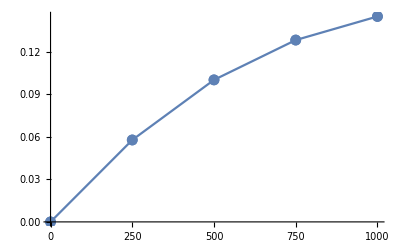

```mathematica
(*pomiki*)
xi=Range[0,L,h];
ListLinePlot[Table[{xi[[i]],Ur[[i]]},{i,1,ele+1}],Mesh->Full]
```

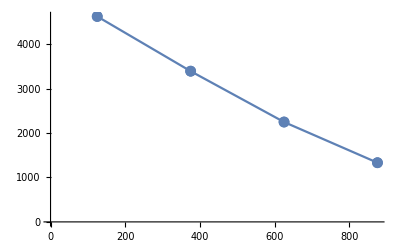

```mathematica
(*notranja osna sila*)
Ni=Table[0,{i,1,ele}];
For[i=1,i≤ ele,i++,
Ni[[i]]=Ej A/h(-Ur[[i]]+Ur[[i+1]])
]

ListLinePlot[Table[{(i-1)h+h/2,Ni[[i]]},{i,1,ele}],Mesh->Full]
```

## 3. Naloga

(Naloga #4 v dokumentu)
Prikazani osno obremenjeni element obravnavaj po MKE. Uporabi dvovozliščne KE.
Določi ter izriši vozliščne vrednosti pomika ter notranje osne sile.

```mathematica
L=1000.;
n0=5.;
A=100.;
Ej=200000.;
F=1000.;

nx[x_]=n0 (0.5+0.1 Cos[4 x/L π]);
Kele[Ee_,Ae_,Le_]=(Ee Ae)/Le ({{1, -1}, {-1, 1}});
```

```mathematica
ele=4;
h=L/ele;
n=ele+1;

Ke=Table[0,{i,1,n},{j,1,n}];
Ff=Fn=Table[0,{i,1,n}];
For[i=1,i≤ ele,i++,
Ke[[{i,i+1},{i,i+1}]]+=Kele[Ej,A,h];
xi=(i-1)h;
Fn1=Integrate[nx[xi+x] (1-x/h),{x,1,h}];
Fn2=Integrate[nx[xi+x] (x/h),{x,1,h}];
Fn[[{i,i+1}]]+={Fn1,Fn2};
 ]

U=Table[Subscript[u, i],{i,1,n}];

U[[1]]=0;
Ff[[1]]=Ra;
Ff[[-1]]=F;

Print[MatrixForm[Ke],MatrixForm[U],MatrixForm[Ff],MatrixForm[Fn]]

s=Solve[Ke.U==Ff+Fn];
Ur=U/.s[[1]];
Ur=Flatten[Ur]
```

(80000. | -80000. | 0 | 0 | 0
-80000. | 160000. | -80000. | 0 | 0
0 | -80000. | 160000. | -80000. | 0
0 | 0 | -80000. | 160000. | -80000.
0 | 0 | 0 | -80000. | 80000.)(0
u_2
u_3
u_4
u_5)(Ra
0
0
0
1000.)(334.836
572.337
672.663
572.337
337.826)

{0,0.0394395,0.0717249,0.0956019,0.112325}

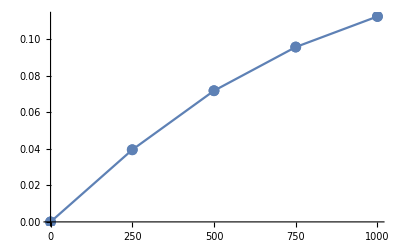

```mathematica
xi=Range[0,L,h];
ListLinePlot[Table[{xi[[i]],Ur[[i]]},{i,1,ele+1}],Mesh->Full]
```

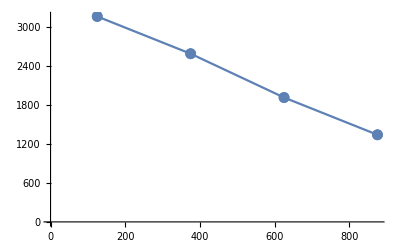

```mathematica
Ni=Table[0,{i,1,ele}];
For[i=1,i≤ ele,i++,
Ni[[i]]=Ej A/h (-Ur[[i]]+Ur[[i+1]])
]
ListLinePlot[Table[{(i-1)h+h/2,Ni[[i]]},{i,1,ele}],Mesh->Full]
```

## Priprave za vajo 8

- obravnava problema prevoda toplote: enodimenzijski (1d) in casovno ustaljeni primeri prevoda toplote (eno polje in vec polj)
- zapis (in razumevanje) robnih pogojev in pogojev prehoda
- resevanje 1d casovno ustaljenega problema prevoda toplote analiticno in po MKR

## 1. Naloga

Enodimenzijski časovno ustaljen problem prevoda toplote -- eno polje. Rešimo analitično in z MKR.

```mathematica
T0=20(*oC*);
Tok=-10(*oC*);
k=0.5(*W/m K*);
α=10(*W/m^2 K*);
L=0.5(*m*);
```

### Analitično

```mathematica
Clear[T]
d=DSolve[{
T''[x]==0,
T[0]==T0,-k T'[L]==α (T[L]-Tok)},T[x],x]
T[x_]=T[x]/.d[[1]];
```

{{T[x]→(k T0+L T0 α-T0 x α+Tok x α)/(k+L α)}}

### MKR

```mathematica
(*Definiramo korak*)
del=10;
h=L/del;
n=del+3;
(*Matrika in vektor znank*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*Robni pogoji*)
M[[1,2]]=1;
b[[1]]=T0;
M[[2,{-3,-2,-1}]]={k/(2h),-α,-k/(2h)};
b[[2]]=-α Tok;
(*DE*)
For[i=1,i≤n-2,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1};
]
(*Rešimo sistem linearnih enačb*)
Ti=LinearSolve[M,b];

Print[MatrixForm[M],"=",MatrixForm[b]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5. | -10 | -5.
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)=(20
100
0
0
0
0
0
0
0
0
0
0
0)

### Primerjava analitične in MKR metode

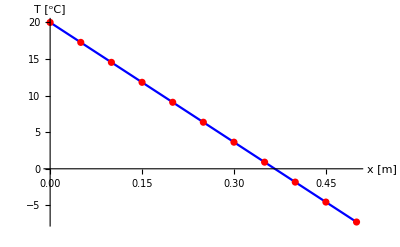

```mathematica
p1=Plot[T[x],{x,0,L},PlotStyle->Blue];
p2=ListPlot[Table[{(i-1)h,Ti[[i+1]]},{i,1,n-2}],PlotStyle->Red];
Show[p1,p2,AxesLabel-> {"x [m]","T [^oC]"}]
```

## 2. Naloga

Za dani časovno ustaljeni problem prevoda toplote določi porazdelitev temperaure skozi steno. Nalogo reši analitično in po MKR.

```mathematica
{Tn,Tok}={20,-5}(*oC*);
{α1,α2}={2,20}(*W/m^2K*);
{k1,k2}={0.5,0.05}(*W/m K*);
{L1,L2}={0.5,0.1}(*m*);
Q0=100(*W/m^3*);
```

### Analitično

```mathematica
Clear[T1,T2]
d=DSolve[{
qv[x_]=Q0 (4x)/L1^2(L1-x);
k1 T1''[x]==-qv[x],k2 T2''[x]==0,
k1 T1'[0]==α1 (T1[0]-Tn),-k2 T2'[L1+L2]==α2(T2[L1+L2]-Tok),
T1[L1]==T2[L1], -k1 T1'[L1]==-k2 T2'[L1]
},{T1[x],T2[x]},x]
{T1[x_],T2[x_]}={T1[x],T2[x]}/.d[[1]];
```

{{T1[x]→28.4507+33.8028 x-266.667 x^3+266.667 x^4,T2[x]→193.005-328.638 x}}

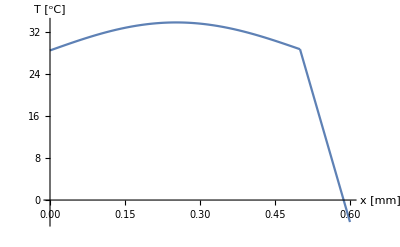

```mathematica
p11=Plot[T1[x],{x,0,L1}, AxesOrigin->{0,0}];
p12=Plot[T2[x],{x,L1,L1+L2}];
Show[p11,p12,PlotRange-> All, AxesLabel-> {"x [mm]","T [^oC]"}]
```

### MKR

```mathematica
qv[x_]=Q0 (4x)/L1^2(L1-x);
(*Definirajmo korake*)
{del1,del2}={3,3};
{n1,n2}={del1+3,del2+3};
{h1,h2}={L1/del1,L2/del2};
(*Matrika koeficientov M in vektor znanih vrednosti b*)
M=Table[0,{i,1,n1+n2},{j,1,n1+n2}];
b=Table[0,{i,1,n1+n2}];
(*RP*)
M[[1,{1,2,3}]]={k1/(2h1),α1,-k1/(2h1)};
b[[1]]=α1 Tn;
M[[2,{-3,-2,-1}]]={k2/(2h2),-α2,-k2/(2h2)};
b[[2]]=-α2 Tok;
(*PKP*)
M[[3,{n1-1,n1+2}]]={1,-1};
M[[4,{n1-2,n1-1,n1,n1+1,n1+2,n1+3}]]=-k1 {-1,0,1,0,0,0}/(2 h1)+k2{0,0,0,-1,0,1}/(2 h2);
(*DE*)
For[i=1,i≤ del1+1,i++,
M[[i+4,{i,i+1,i+2}]]={1,-2,1};
b[[i+4]]=-qv[(i-1)h1] h1^2/k1;
]
For[i=1,i≤ del2+1,i++,
M[[n1+i+2,{i+n1,i+n1+1,i+n1+2}]]={1,-2,1};
b[[n1+i+2]]=0;
]
(*Rešimo sistem enačb*)
Ti=LinearSolve[M,b]
Print[MatrixForm[M],MatrixForm[Ti],"=",MatrixForm[b]]
```

{22.3735,27.1205,31.8675,31.6762,26.5467,21.4171,36.8058,26.5467,16.2876,6.02852,-4.23057,-14.4897}

(1.5 | 2 | -1.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.75 | -20 | -0.75
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 0. | -1.5 | -0.75 | 0. | 0.75 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)(22.3735
27.1205
31.8675
31.6762
26.5467
21.4171
36.8058
26.5467
16.2876
6.02852
-4.23057
-14.4897)=(40
100
0
0
0.
-4.93827
-4.93827
0.
0
0
0
0)

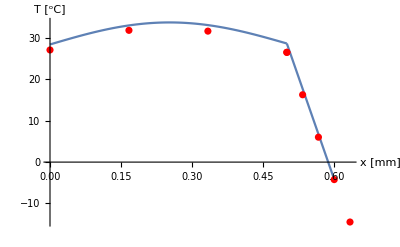

```mathematica
p21=ListPlot[Table[{(i-1)h1,Ti[[i+1]]},{i,1,n1-2}],PlotStyle->Red];
p22=ListPlot[Table[{L1+(i-1)h2,Ti[[n1+i+1]]},{i,1,n2-1}],PlotStyle->Red];

Show[p11,p12,p21,p22,PlotRange-> All,AxesLabel-> {"x [mm]","T [^oC]"}]
```

## 3. Naloga

Enodimenzijski časovno ustaljen problem prevoda toplote -- primer za k = k(x). Problem reši analitično in po MKR.

```mathematica
T0=100;
Tok=20;
α=10;
{k0,dk}={20,15};
L=1;
```

### Analitično

```mathematica
Clear[T,k]
d=DSolve[{
k[x_]=k0-dk/L x;
k'[x] T'[x]+k[x]T''[x]==0,
T[0]==T0,
-k[L]T'[L]==α(T[L]-Tok)
},T[x],x]
T[x_]=T[x]/.d[[1]];
```

{{T[x]→(20 (15+2 Log[4]+8 Log[4-3 x]))/(3+2 Log[4])}}

### MKR

```mathematica
del=50;
h=L/del;
n=del+3;

k[x_]=k0-dk/L x;

M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];

M[[1,2]]=1;
b[[1]]=T0;
M[[2,{-3,-2,-1}]]=-k[L] {-1,0,1}/(2h)-α {0,1,0};
b[[2]]=-α Tok;
For[i=1,i≤del+1,i++,
M[[i+2,{i,i+1,i+2}]]=k'[(i-1)h]/(2h) {-1,0,1}+k[(i-1)h]/h^2 {1,-2,1};
]

Ti=LinearSolve[M,b];

(*Print[MatrixForm[M],MatrixForm[b]]*)
```

### Primerjava

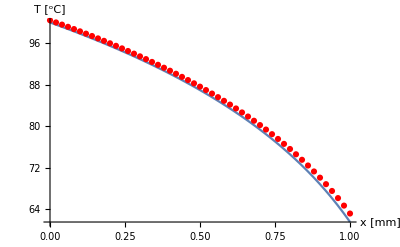

```mathematica
p1=Plot[T[x],{x,0,L}];
p2=ListPlot[Table[{(i-1)h,Ti[[i]]},{i,1,del+1}],PlotStyle->Red];
Show[p1,p2,AxesLabel-> {"x [mm]","T [^oC]"}]
```

## 4. Naloga

Obravnavaj prikazan primer enodimenzijskega časovno-ustaljenega prevoda toplote. 
Obravnavaj prikazan primer analitično in po MKR za poljubno delitev mreže. problem ima dve polji.

```mathematica
(*Podatki; Enote: m, W, K*)
```

```mathematica
{L1,L2}={0.1,0.5};
{k1,k2}={0.06,0.8};
Tok=-5;
α=15;
Tn=20.;
```

### Analitično

```mathematica
Clear[T1,T2]
d=DSolve[{
k1 T1''[x]==0,k2 T2''[x]==0,
k1 T1'[0]==α(T1[0]-Tok),T2[L1+L2]==Tn,
T1[L1]==T2[L1], k1 T1'[L1]==k2 T2'[L1]
},{T1[x],T2[x]},x]
{T1[x_],T2[x_]}={T1[x],T2[x]}/.d[[1]];

p11=Plot[T1[x],{x,0,L1}];
p12=Plot[T2[x],{x,L1,L1+L2}];
```

{{T1[x]→-4.29329+176.678 x,T2[x]→12.0495+13.2509 x}}

### MKR

```mathematica
{del1,del2}={10,20};
{h1,h2}={L1/del1,L2/del2};

M=Table[0,{i,1,del1+del2+6},{j,1,del1+del2+6}];
b=Table[0,{i,1,del1+del2+6}];

(*RP*)
M[[1,{1,2,3}]]=k1/(2h1){-1,0,1}-α{0,1,0};
b[[1]]=-α Tok;
M[[2,-2]]=1;
b[[2]]=Tn;
(*PKP*)
M[[3,{del1+2,del1+5}]]={1,-1};
M[[4,{del1+1,del1+2,del1+3,del1+4,del1+5,del1+6}]]=k1/(2h1){-1,0,1,0,0,0}-k2/(2h2){0,0,0,-1,0,1};
(*DE*)
For[i=1,i≤ del1+1,i++,
M[[i+4,{i,i+1,i+2}]]=k1/h1^2 {1,-2,1};
]
For[i=1,i≤ del2+1,i++,
M[[i+4+del1+1,{i+del1+3,del1+i+4,del1+i+5}]]=k2/h2^2 {1,-2,1};
]

(*Rešitev*)
Ti=LinearSolve[M,b]

(*Print[MatrixForm[M],MatrixForm[b]]*)
```

{-6.06007,-4.29329,-2.5265,-0.759717,1.00707,2.77385,4.54064,6.30742,8.0742,9.84099,11.6078,13.3746,15.1413,13.0433,13.3746,13.7058,14.0371,14.3684,14.6996,15.0309,15.3622,15.6935,16.0247,16.356,16.6873,17.0186,17.3498,17.6811,18.0124,18.3436,18.6749,19.0062,19.3375,19.6687,20.,20.3313}

### prikaz

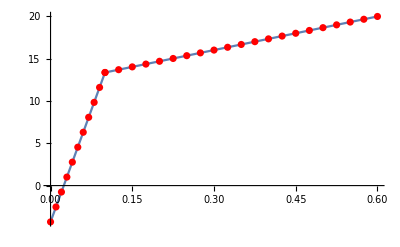

```mathematica
p21=ListPlot[Table[{(i-1)h1,Ti[[i+1]]},{i,1,del1+1}],PlotStyle->Red];
p22=ListPlot[Table[{L1+(i-1)h2,Ti[[i+del1+4]]},{i,1,del2+1}],PlotStyle->Red];
Show[p11,p12,p21,p22,PlotRange-> All]
```

## Priprave za vajo 9

- obravnava problema prevoda toplote vzdolz rebra (analiticno, MKR, MKE)
- obravnava problema z uporabo trovozliscnih koncnih elementov (KE)

## Naloga 1

Za prikazano rebro izračunaj porazdelitev temperature vzdolž rebra. Problem obravnavaj po MKR in MKE (dvo in tro-vozliščni KE).

```mathematica
T0=100.(*oC*);
Tok=20.(*oC*);
α=10.(*W/m^2K*);
k=50.(*W/m K*);
L=0.1(*m*);
t=3 10^-3(*m*);
b=0.05(*m*);

P=2 (t+b);
A=t b;
H=(P α)/(A k);
```

### Analitično

```mathematica
Clear[T]
DSolve[{T''[x]-H (T[x]-Tok)==0,T[0]==T0,-k T'[L]==α(T[L]-Tok)},T[x],x];
T[x_]=T[x]/.%[[1]]
```

6.58506 ⅇ^(-11.8884 x) (11.1487+3.03718 ⅇ^(11.8884 x)+1. ⅇ^(23.7767 x))

### MKR

```mathematica
del=4;
h=L/del;

M=Table[0,{i,1,del+3},{j,1,del+3}];
bi=Table[0,{i,1,del+3}];

M[[1,2]]=1;
bi[[1]]=T0;
M[[2,{-3,-2,-1}]]={1,-2h α/k,-1};
bi[[2]]=-2 h α/k Tok;

For[i=1,i≤del+1,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2,1}/h^2-H {0,1,0};
bi[[i+2]]=-H Tok;
]
Ti=LinearSolve[M,bi]
```

{123.581,100.,83.4857,72.5793,66.3173,64.1468,65.8759}

### MKE (dvo-vozliščen KE)

```mathematica
ele=3;
h2=L/ele;
n=ele+1;

(*Definiramo matriko, vektorje in dele matrik*)
Kc=Table[0,{i,1,n},{j,1,n}];
qi=Ci=Table[0,{i,1,n}];
Tc=Table[Subscript[T, i],{i,1,n}];
M11=M22=k/h2+H k h2/3;
M12=-k/h2+H k h2/6;
C1=H k h2 Tok/2;
(*RP*)
Tc[[1]]=T0;
qi[[1]]=qv;
qi[[n]]=-α (Subscript[T, n]-Tok);
(*KE v glob sist.*)
For[i=1,i≤ele,i++,
Kc[[{i,i+1},{i,i+1}]]+=({{M11, M12}, {M12, M22}});
Ci[[{i,i+1}]]+=C1 {1,1};]
Print[MatrixForm[Kc],MatrixForm[Tc],"=",MatrixForm[qi],"+",MatrixForm[Ci]]

Solve[Kc.Tc==qi+Ci]
Tc=Tc/.Flatten[%];
```

(1578.52 | -1460.74 | 0 | 0
-1460.74 | 3157.04 | -1460.74 | 0
0 | -1460.74 | 3157.04 | -1460.74
0 | 0 | -1460.74 | 1578.52)(100.
T_2
T_3
T_4)=(qv
0
0
-10. (-20.+T_4))+(2355.56
4711.11
4711.11
2355.56)

{{qv→40096.2,T_2→79.0011,T_3→67.5165,T_4→63.6944}}

### MKE (tro-vozliščni KE)

```mathematica
ele=3;
h3=L/ele;
n3=2ele+1;
(*Definiramo matriko, vektorje*)
Kc=Table[0,{i,1,n3},{i,1,n3}];
qi=Ci=Table[0,{i,1,n3}];
Tc2=Table[Subscript[T, i],{i,1,n3}];
(*Deli matrike koef.*)
H2=(P α)/A;
C1=(H2 h3 Tok)/6;
M11=(7k)/(3h3)+(4H2 h3)/30;
M22=(16k)/(3h3)+(16H2 h3)/30;
M12=-(8k)/(3h3)+(2H2 h3)/30;
M13=k/(3h3)-(H2 h3)/30;
(*RP*)
Tc2[[1]]=T0;
qi[[1]]=qr;
qi[[n3]]=-α(Subscript[T, n3]-Tok);
(*For loop*)
For[i=1,i≤ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2},{j,j+1,j+2}]]+=({{M11, M12, M13}, {M12, M22, M12}, {M13, M12, M11}});
Ci[[{j,j+1,j+2}]]+=C1{1,4,1};
]
Print[MatrixForm[Kc],MatrixForm[Tc2],"=",MatrixForm[qi],"+",MatrixForm[Ci]]
Solve[Kc.Tc2==qi+Ci]
Tc2=Tc2/.Flatten[%];
```

(3531.41 | -3984.3 | 492.148 | 0 | 0 | 0 | 0
-3984.3 | 8125.63 | -3984.3 | 0 | 0 | 0 | 0
492.148 | -3984.3 | 7062.81 | -3984.3 | 492.148 | 0 | 0
0 | 0 | -3984.3 | 8125.63 | -3984.3 | 0 | 0
0 | 0 | 492.148 | -3984.3 | 7062.81 | -3984.3 | 492.148
0 | 0 | 0 | 0 | -3984.3 | 8125.63 | -3984.3
0 | 0 | 0 | 0 | 492.148 | -3984.3 | 3531.41)(100.
T_2
T_3
T_4
T_5
T_6
T_7)=(qr
0
0
0
0
0
-10. (-20.+T_7))+(785.185
3140.74
1570.37
3140.74
1570.37
3140.74
785.185)

{{qr→39725.3,T_2→88.2464,T_3→79.1827,T_4→72.4484,T_5→67.7812,T_6→64.9947,T_7→63.9816}}

### Primerjava metod

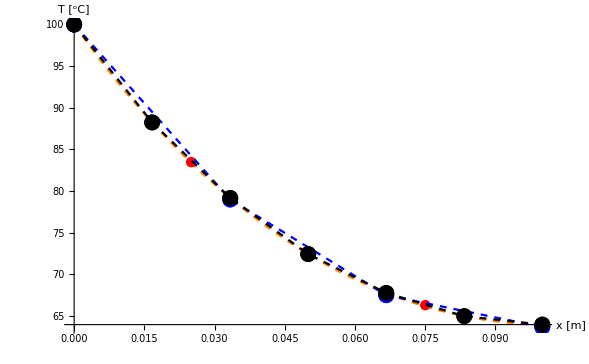

```mathematica
pAna=Plot[T[x],{x,0,L},PlotStyle->{Orange,Dashed}];
pMKR=ListPlot[Table[{(i-1)h,Ti[[i+1]]},{i,1,del+1}],PlotStyle->{Red,Dashed}];
pMKE2=ListLinePlot[Table[{(i-1)h2,Tc[[i]]},{i,1,n}],PlotStyle->{Blue,Dashed},Mesh->Full];
pMKE3=ListLinePlot[Table[{(((i-1)/2))h3,Tc2[[i]]},{i,1,n3}],PlotStyle->{Black,Dashed},Mesh->Full];
Show[pAna,pMKR,pMKE2,pMKE3,PlotRange-> All,AxesLabel-> {"x [m]","T [^oC]"}]
```

## Naloga 2

```mathematica
(*Enote: m, W, oC*)
d=5 10^-3;
α=10.;
{Ts,Tok}={80.,20.};
{L1,L2}={0.2,0.2};
{k1,k2}={40.,20.};
```

### Analitično

```mathematica
d=5 10^-3;
α=10.;
{Ts,Tok}={80.,20.};
{L1,L2}={0.2,0.2};
{k1,k2}={40.,20.};
P=π d;
A=π d^2/4;

Clear[T1,T2];
d=DSolve[{
T1''[x]-(P α)/(A k1)(T1[x]-Tok)==0,T2''[x]-(P α)/(A k2)(T2[x]-Tok)==0,
T1[0]==Ts,-k2 T2'[L1+L2]==α(T2[L1+L2]-Tok),
T1[L1]==T2[L1], -k1 T1'[L1]==-k2 T2'[L1]
},{T1[x],T2[x]},x]

T1[x_]=T1[x]/.d[[1]];
T2[x_]=T2[x]/.d[[1]];
```

{{T1[x]→0.0360066 ⅇ^(-14.1421 x) (1665.36+555.454 ⅇ^(14.1421 x)+1. ⅇ^(28.2843 x)),T2[x]→0.0000242668 ⅇ^(-20. x) (9.34181×10^6+824171. ⅇ^(20. x)+1. ⅇ^(40. x))}}

### 6/8/10

```mathematica
d=5 10^-3;
α=10.;
{Ts,Tok}={80.,20.};
{L1,L2}={0.2,0.2};
{k1,k2}={40.,20.};

{ele1,ele2}={5,10};
{h1,h2}={L1/ele1,L2/ele2};
n=2ele1+2ele2+1;
(*Matrike, vektorji*)
Mp=Table[0,{i,1,n},{j,1,n}];
qi=Ci=Table[0,{i,1,n}];
Ti=Table[Subscript[T, i],{i,1,n}];
(*Konstante*)
P=π d;
A=π d^2/4;
H=P α/A;
C1[h_]=H h Tok/6;
{M11[k_,h_],M22[k_,h_],M12[k_,h_],M13[k_,h_]}={(7k)/(3h)+(4H h)/30,(16k)/(3h)+(16H h)/30,-(8k)/(3h)+(2H h)/30,k/(3h)-(H h)/30};
(*RP*)
Ti[[1]]=Ts;
qi[[1]]=qv;
qi[[-1]]=-α(Subscript[T, n]-Tok);
(*KE*)
For[i=1,i≤ ele1,i++,
j=2i-1;
Mp[[{j,j+1,j+2},{j,j+1,j+2}]]+=({{M11[k1,h1], M12[k1,h1], M13[k1,h1]}, {M12[k1,h1], M22[k1,h1], M12[k1,h1]}, {M13[k1,h1], M12[k1,h1], M11[k1,h1]}});
Ci[[{j,j+1,j+2}]]+=C1[h1]{1,4,1};
]
For[i=1+ele1,i≤ ele1+ele2,i++,
j=2i-1;
Mp[[{j,j+1,j+2},{j,j+1,j+2}]]+=({{M11[k2,h2], M12[k2,h2], M13[k2,h2]}, {M12[k2,h2], M22[k2,h2], M12[k2,h2]}, {M13[k2,h2], M12[k2,h2], M11[k2,h2]}});
Ci[[{j,j+1,j+2}]]+=C1[h2]{1,4,1};
]

Solve[Mp.Ti==qi+Ci]
Ti=Ti/.%[[1]];
```

{{qv→33902.7,T_2→65.2372,T_3→54.1226,T_4→45.7515,T_5→39.4571,T_6→34.727,T_7→31.1847,T_8→28.5416,T_9→26.5873,T_10→25.1626,T_11→24.1543,T_12→23.4018,T_13→22.7858,T_14→22.2816,T_15→21.869,T_16→21.5314,T_17→21.2553,T_18→21.0295,T_19→20.8451,T_20→20.6945,T_21→20.5719,T_22→20.4721,T_23→20.3914,T_24→20.3263,T_25→20.2744,T_26→20.2334,T_27→20.2018,T_28→20.1783,T_29→20.162,T_30→20.1522,T_31→20.1484}}

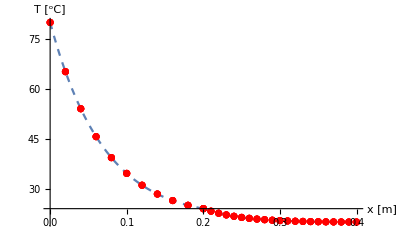

```mathematica
p1a=Plot[T1[x],{x,0,L1},PlotStyle->Dashed];
p2a=Plot[T2[x],{x,L1,L1+L2},PlotStyle->Dashed];
p1mkr=ListPlot[Table[{(i-1)h1/2,Ti[[i]]},{i,1,2ele1+1}],Mesh->Full,PlotStyle->Red];
p2mkr=ListPlot[Table[{L1+(i-1)h2/2,Ti[[i+2ele1]]},{i,1,2ele2+1}],Mesh->Full,PlotStyle->Red];
Show[p1a,p2a,p1mkr,p2mkr,PlotRange-> All,AxesLabel-> {"x [m]","T [^oC]"}]
```

## Naloga 3

```mathematica
t=5 10^-6;
b=0.3;
L1=0.2;
L2=0.2;
Tok=20;
α=10;
Ts=80.;
k1=40.;
k2=20.;

ele1=2;
ele2=2;
h1=L1/ele1;
h2=L2/ele2;
n=2ele1+2ele2+1;

P=2(b+t);
A=b t;
H=P α/A;
C1[h_]=H h Tok/6;
M11[k_,h_]=(7k)/(3h)+(4 H h)/30;
M22[k_,h_]=(16k)/(3h)+(16 H h)/30;
M12[k_,h_]=-(8k)/(3h)+(2 H h)/30;
M13[k_,h_]=k/(3h)-(H h)/30;
(*matrike, vektorji*)
Mp=Table[0,{i,1,n},{j,1,n}];
qi=Ci=Table[0,{i,1,n}];
Ti=Table[Subscript[T, i],{i,1,n}];
(*RP in KE*)
Ti[[1]]=Ts;
qi[[1]]=qv;
Ti[[n]]=-α(Subscript[T, n]-Tok);

For[i=1,i≤ele1,i++,
j=2i-1;
Mp[[{j,j+1,j+2},{j,j+1,j+2}]]+=({{M11[k1,h1], M12[k1,h1], M13[k1,h1]}, {M12[k1,h1], M22[k1,h1], M12[k1,h1]}, {M13[k1,h1], M12[k1,h1], M11[k1,h1]}});
Ci[[{j,j+1,j+2}]]+=C1[h1]{1,4,1};
]
For[i=ele1+1,i≤ele1+ele2,i++,
j=2i-1;
Mp[[{j,j+1,j+2},{j,j+1,j+2}]]+=({{M11[k2,h2], M12[k2,h2], M13[k2,h2]}, {M12[k2,h2], M22[k2,h2], M12[k2,h2]}, {M13[k2,h2], M12[k2,h2], M11[k2,h2]}});
Ci[[{j,j+1,j+2}]]+=C1[h2]{1,4,1};
]
d=Solve[Mp.Ti==qi+Ci];
Ti=Ti/.d[[1]];
Ti=Flatten[Ti];


Print[MatrixForm[Mp],MatrixForm[qi],MatrixForm[Ti],MatrixForm[Ci]]
```

(54267.6 | 25600.4 | -13200.2 | 0 | 0 | 0 | 0 | 0 | 0
25600.4 | 215470. | 25600.4 | 0 | 0 | 0 | 0 | 0 | 0
-13200.2 | 25600.4 | 108535. | 25600.4 | -13200.2 | 0 | 0 | 0 | 0
0 | 0 | 25600.4 | 215470. | 25600.4 | 0 | 0 | 0 | 0
0 | 0 | -13200.2 | 25600.4 | 108068. | 26133.8 | -13266.9 | 0 | 0
0 | 0 | 0 | 0 | 26133.8 | 214404. | 26133.8 | 0 | 0
0 | 0 | 0 | 0 | -13266.9 | 26133.8 | 107602. | 26133.8 | -13266.9
0 | 0 | 0 | 0 | 0 | 0 | 26133.8 | 214404. | 26133.8
0 | 0 | 0 | 0 | 0 | 0 | -13266.9 | 26133.8 | 53800.9)(qv
0
0
0
0
0
0
0
0)(80.
11.711
29.7659
18.6494
21.6019
19.7712
20.2749
19.9556
20.0893)(1.33336×10^6
5.33342×10^6
2.66671×10^6
5.33342×10^6
2.66671×10^6
5.33342×10^6
2.66671×10^6
5.33342×10^6
1.33336×10^6)

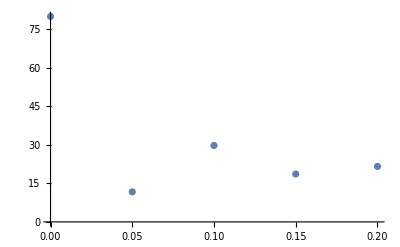

```mathematica
ListPlot[Table[{(i-1)h1/2,Ti[[i]]},{i,1,2ele1+1}]]
```

## Priprave za vajo 10

- obravnava enodimenzijskega časovno odvisnega problema prevoda toplote po MKR
- rečevanje časovno odvisnega problema z uporabo implicitne in eksplicitne časovne sheme
- reševanje (programiranje) časovno odvisnih problemov (po MKR) v Mathematici

## Naloga 1

Določi čas, po katerem se v steni vzpostavi stacionarno temperaturno stanje. Temp. stene pri času t=0 je Tz. Problem rešuj po MKR za: 
a) Eksplicitno shemo
b) Implicitno shemo

```mathematica
(*Podatki*)
Tok=-5;(*oC*)
Tn=20.;(*oC*)
Tz=5.;(*oC*)
α=10.;(*W/mK*)
k=0.8;(*W/m^2K*)
ρ=2400.;(*kg/m^3*)
cp=0.8 10^3;(*J/kg K*)
L=0.5;(*m*)
c=cp ρ/k;
```

### Eksplicitna časovna shema

#### Fiksni korak mreže in ročna iteracija

```mathematica
(*Diskretizacija*)
del=3;
h=L/del;
dt=(ρ cp h^2)/(2k)*0.1;
(*začetno stanje*)
Ti=Table[Tz,{i,1,5}];
Ti[[1]]=Tn;
Ti[[5]]=-2h α/k (Ti[[4]]-Tok)+Ti[[3]];
j=0;
```

T=(20.
10.99
4.27012
-1.98425
-8.29552)^oC  Čas:  t=15.7407h;  Iteracija: 17   Razlika: 0.00689499

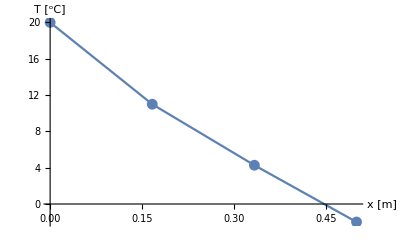

```mathematica
(*Nadaljni časi*)
To=Ti;
Ti[[1]]=Tn;
Ti[[2]]=dt/(c h^2)(To[[3]]-2To[[2]]+To[[1]])+To[[2]];
Ti[[3]]=dt/(c h^2)(To[[4]]-2To[[3]]+To[[2]])+To[[3]];
Ti[[4]]=dt/(c h^2)(To[[5]]-2To[[4]]+To[[3]])+To[[4]];
Ti[[5]]=-2h α/k (Ti[[4]]-Tok)+Ti[[3]];
j+=1;

Print["T=",MatrixForm[Ti],"^oC","  Čas:  t=",j dt/3600,"h;  Iteracija: ",j, "   Razlika: ",Abs[Ti[[4]]-To[[4]]]]
ListLinePlot[Table[{(i-1)h,Ti[[i]]},{i,1,4}],AxesLabel->{"x [m]","T [^oC]"}, Mesh->All]
```

#### Poljubni korak mreže ter avtomatska iteracija

```mathematica
(*Diskretizacija*)
del=12;
h=L/del;
dt=(ρ cp h^2)/(2k)*0.3;
n=del+2;
e=0.0001;
(*začetno stanje*)
Ti=Table[Tz,{i,1,n}];
Ti[[1]]=Tn;
Ti[[n]]=-2h α/k (Ti[[n-1]]-Tok)+Ti[[n-2]];
Tskup={};
j=0;
```

```mathematica
(*Nadaljni časi*)
nt=0;
For[j=1,j≤ j+1,j++,
Tskup=Join[Tskup,{Ti}];
To=Ti;
Ti[[1]]=Tn;
For[i=1,i≤ del,i++,
Ti[[i+1]]=dt/(c h^2)(To[[i+2]]-2To[[i+1]]+To[[i]])+To[[i+1]];
];
Ti[[n]]=-2h α/k (Ti[[n-1]]-Tok)+Ti[[n-2]];
nt+=1;
If[Abs[Ti[[n-1]]-To[[n-1]]]<e,
Break[]]
]
```

```mathematica
Print["čas ustalitve je t= ",j dt/3600," s. Potrebno je bilo ",j," iteracij.", nt]
MatrixForm[Tskup];
Manipulate[
ListLinePlot[Table[{(i-1)h,Tskup[[j,i]]},{i,1,n-1}],AxesLabel->{"x [m]","T [^oC]"}, Mesh->All,PlotRange->All],{j,1,nt,1}]
```

čas ustalitve je t= 18.4028 s. Potrebno je bilo 106 iteracij.106

### Implicitna časovna shema

#### Fiksni korak mreže in ročna iteracija

```mathematica
del=3;
h=L/del;
dt=1 3600(*s*);
```

```mathematica
(*začetno stanje*)
Ti=Table[Tz,{i,1,5}];
j=0;
```

{{5.,5.,5.,5.,5.},{20.,5.72876,4.95307,3.30828,-29.6647}}

(1 | 0 | 0 | 0 | 0
0 | 0 | 2.4 | -10. | -2.4
1 | -20.5185 | 1 | 0 | 0
0 | 1 | -20.5185 | 1 | 0
0 | 0 | 1 | -20.5185 | 1)(20.
6.38295
4.88046
2.03328
-24.4249)=(20.
50.
-106.088
-91.7235
-61.2644)  t = 2

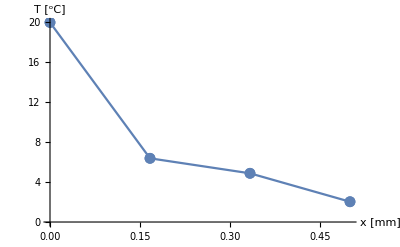

```mathematica
(*nadaljni časi*)
To=Ti;

M=({{1, 0, 0, 0, 0}, {0, 0, k/(2h), -α, -k/(2h)}, {1, -2-(c h^2)/dt, 1, 0, 0}, {0, 1, -2-(c h^2)/dt, 1, 0}, {0, 0, 1, -2-(c h^2)/dt, 1}});
b=({{Tn}, {-α Tok}, {-(c h^2)/dt To[[2]]}, {-(c h^2)/dt To[[3]]}, {-(c h^2)/dt To[[4]]}});
Ti=LinearSolve[M,b]//Flatten;

j++;

Print[MatrixForm[M],MatrixForm[Ti],"=",MatrixForm[b],"  t = ",dt*j/3600]
ListLinePlot[Table[{(i-1)h,Ti[[i]]},{i,1,4}],PlotRange->All,Mesh->Full,AxesLabel->{"x [mm]","T [^oC]"}]
```

#### Poljubni korak mreže ter avtomatska iteracija

```mathematica
del=100;
h=L/del;
n=del+2;

dt=0.3 3600(*s*);
tn=300;

(*začetno stanje*)
Ti=Table[Tz,{i,1,n}];
Tskup={Ti};
j=1;
```

```mathematica
(*nadaljni časi*)
M=Table[0,{i,1,n},{i,1,n}]; (*Ustvarimo matriko in vektor*)
b=Table[0,{i,1,n}];

M[[1,1]]=1;(*Robni pogoji*)
b[[1]]=Tn;
M[[2,{-3,-2,-1}]]={k/(2h),-α,-k/(2h)};
b[[2]]=-α Tok;

For[j=2,j≤tn,j++,
To=Ti;
For[i=1,i≤ del,i++,(*DE*)
M[[i+2,{i,i+1,i+2}]]={1,-2-(c h^2)/dt,1};
b[[i+2]]=-(c h^2)/dt To[[i+1]];
];
Ti=LinearSolve[M,b]//Flatten;
Tskup=Join[Tskup,{Ti}];
]
Print["t = ",dt*(j-1)/3600, " h, pri ",j-1," iteracijah"]
Manipulate[
ListLinePlot[Table[{(i-1)h,Tskup[[j,i]]},{i,1,n-1}],PlotRange->All,Mesh->None,AxesLabel->{"x [mm]","T [^oC]"}]
,{j,1,tn,1}]
```

t = 90. h, pri 300 iteracijah

## Naloga 2

Določi (približni) čas t_s [h], po katerem se v steni vzpostavi časovno ustaljeno stanje. V začetnem stanju je temperatura skozi steno konstantna, enaka Tz. Izriši temperaturni profil skozi steno pri času t = 5h ter v časovno ustaljenem stanju.

```mathematica
L=0.4;
Tok=-10.;
Tn=20.;
Tz=0.;
α=20.;
k=0.9;
ρ=3000.;
cp=8000.;
c=(ρ cp)/k;
```

### Ocena 8

Nalogo reši za delitev mreže h = L/5. Čas tS lahko določiš “ročno” (z zaporednim (posamičnem) zaganjanjem kode).

```mathematica
del=5;
h=L/del;
n=del+3;

dt=100*3600(*h*);

(*začetni čas*)
Ti=Table[Tz,{i,1,n}];
j=0;
```

(5.625 | 20. | -5.625 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5.625 | -20. | -5.625
1 | -2.47407 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2.47407 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2.47407 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2.47407 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2.47407 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2.47407 | 1)(27.9616
14.0437
6.78346
2.73914
-0.00663585
-2.75555
-6.81081
-14.0949)=(400.
200.
0.
0.
0.
0.
0.
0.)    t_s = 100

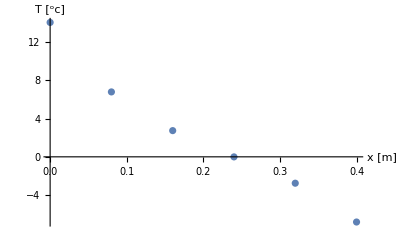

```mathematica
(*nadaljni časi*)
To=Ti;

M=({{k/(2h), α, -k/(2h), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, k/(2h), -α, -k/(2h)}, {1, -2-(c h^2)/dt, 1, 0, 0, 0, 0, 0}, {0, 1, -2-(c h^2)/dt, 1, 0, 0, 0, 0}, {0, 0, 1, -2-(c h^2)/dt, 1, 0, 0, 0}, {0, 0, 0, 1, -2-(c h^2)/dt, 1, 0, 0}, {0, 0, 0, 0, 1, -2-(c h^2)/dt, 1, 0}, {0, 0, 0, 0, 0, 1, -2-(c h^2)/dt, 1}});
b=({{α Tn}, {-α Tok}, {-(c h^2)/dt To[[2]]}, {-(c h^2)/dt To[[3]]}, {-(c h^2)/dt To[[4]]}, {-(c h^2)/dt To[[5]]}, {-(c h^2)/dt To[[6]]}, {-(c h^2)/dt To[[7]]}});
Ti=LinearSolve[M,b]//Flatten;
j++;

Print[MatrixForm[M],MatrixForm[Ti],"=",MatrixForm[b], "    t_s = ",dt/3600*j]
ListPlot[Table[{(i-1)h,Ti[[i+1]]},{i,1,n-2}],PlotRange->All,AxesLabel->{"x [m]","T [^oc]"}]
```

### Ocena 10

Nalogo reši za poljuben korak mreže. Čas tS naj bo določen samodejno z Mathematico.

```mathematica
del=3;
h=L/del;
n=del+3;

dt=5*3600(*h*);
tn=200;
j=1;
e=0.001;

(*začetni čas*)
Ti=Table[Tz,{i,1,n}];
Tskup={Ti};
```

```mathematica
(*nadaljni časi*)
M=Table[0,{i,1,n},{i,1,n}];
b=Table[0,{i,1,n}];

M[[1,{1,2,3}]]={k/(2h),α,-k/(2h)};
b[[1]]=α Tn;
M[[2,{-3,-2,-1}]]={k/(2h),-α,-k/(2h)};
b[[2]]=-α Tok;
For[j=2,j≤tn,j++,
To=Ti;

For[i=1,i≤del+1,i++,
M[[i+2,{i,i+1,i+2}]]={1,-2-(c h^2)/dt,-1};
b[[i+2]]=-(c h^2)/dt To[[i+1]];
];
Ti=LinearSolve[M,b]//Flatten;
Tskup=Join[Tskup,{Ti}];
]

Print[MatrixForm[M],MatrixForm[Ti],"=",MatrixForm[b], "    t_s = ",dt/3600*j]

Manipulate[ListPlot[Table[{(i-1)h,Tskup[[j,i+1]]},{i,1,n-3}],PlotRange->All,AxesLabel->{"x [m]","T [^oc]"}],{j,1,tn,1}]
```

(3.375 | 20. | -3.375 | 0 | 0 | 0
0 | 0 | 0 | 3.375 | -20. | -3.375
1 | -28.3374 | -1 | 0 | 0 | 0
0 | 1 | -28.3374 | -1 | 0 | 0
0 | 0 | 1 | -28.3374 | -1 | 0
0 | 0 | 0 | 1 | -28.3374 | -1)(3.72797×10^13
14.9531
3.72797×10^13
-2.20917×10^14
1.34642×10^15
-8.19968×10^15)=(400.
200.
-393.827
-8.35495×10^14
4.95108×10^15
-3.01752×10^16)    t_s = 1005

## Priprave za vajo 11

Kolokvij

## Priprave za vajo 12

- obravnava primerov upogiba nosilca (analiticno in po MKR) z uporabo diferencialne enacbe upogiba 4. reda
- poznavanje diferencialne enacbe upogiba 4. reda ter dolocitev robnih pogojev
- dolocitev notranjega upogibnega momenta iz funkcije upogibnice nosilca (analiticno in po MKR)
- dolocitev reakcij iz funkcije upogibnice nosilca (analiticno in po MKR)

## Naloga 1

Obravnavaj problem upogiba nosilca analitično in po MKR. Določi poves nosilca, potek notranjih veličin in velikosti reakcij.

```mathematica
(*podatki*)
L=2 10^3(*mm*);
M0=3 10^6(*Nmm*);
F0=2 10^3(*N*);
Ej=200000.(*MPa*);
Iu=171 10^4(*mm^4*);
{q1,q2}={5,2}(*N/mm*);
qx[x_]=q1-(q1-q2)/L x;
```

### Analitično

```mathematica
(*Reševanje dif. en. za določitev funkcije povesa*)
Clear[w]
DSolve[{
w''''[x]==qx[x]/(Ej Iu),
w[0]==0,w'[0]==0,
-w'''[L] Ej Iu==F0,-w''[L]Ej Iu==M0},w[x],x];
w[x_]=w[x]/.%[[1]]
```

0.0000102339 x^2-4.38596×10^-9 x^3+6.09162×10^-13 x^4-3.65497×10^-17 x^5

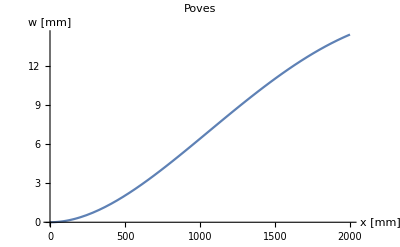

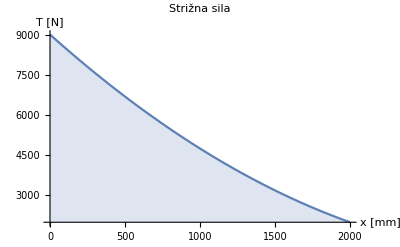

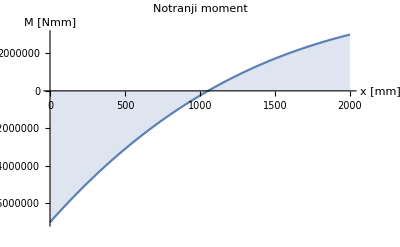

```mathematica
(*izris povesa, notranje strižne sile in notranjega momenta*)
Plot[w[x],{x,0,L},PlotLabel-> "Poves",AxesLabel->{"x [mm]","w [mm]"}]
Plot[-w'''[x]Ej Iu,{x,0,L},PlotLabel-> "Strižna sila",AxesLabel->{"x [mm]","T [N]"},Filling->Axis]
Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel-> "Notranji moment",AxesLabel->{"x [mm]","M [Nmm]"},Filling->Axis]
```

```mathematica
(*Določitev reakcij iz funkcije povesa nosilca*)
Az=-w'''[0]Ej Iu;
Ma=w''[0]Ej Iu;
Print["strižna sila Az=",Az,"N in reakcijski moment ","Ma=",Ma,"Nmm"]
```

strižna sila Az=9000.N in reakcijski moment Ma=7.×10^6Nmm

### MKR

{1.85497,0.408187,-1.05471×10^-15,0.408187,1.43392,2.90035,4.65123,6.54947,8.47579,10.3273,12.0159,13.4674,14.6194,15.4206,15.8288}

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 0 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(1.85497
0.408187
-1.05471×10^-15
0.408187
1.43392
2.90035
4.65123
6.54947
8.47579
10.3273
12.0159
13.4674
14.6194
15.4206
15.8288)=(0
0
0.0935673
0.350877
0.0233918
0.0219883
0.0205848
0.0191813
0.0177778
0.0163743
0.0149708
0.0135673
0.0121637
0.0107602
0.00935673)

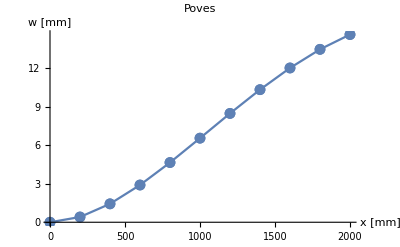

```mathematica
(*diskretizacija*)
del=10;
h=L/del;
n=del+5;
(*definiramo matriko, vektorje*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,3]]=1;
M[[2,{2,4}]]={-1,1};
M[[3,{-5,-4,-3,-2,-1}]]={1,-2,0,2,-1};
b[[3]]=2 h^3 F0/(Ej Iu);
M[[4,{-4,-3,-2}]]={-1,2,-1};
b[[4]]=h^2 M0/(Ej Iu);
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=h^4 qx[(i-1)h]/(Ej Iu);
]
wi=LinearSolve[M,b]
Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]]
(*izris povesa*)
ListLinePlot[Table[{(i-1)h,wi[[i+2]]},{i,1,n-4}],AxesLabel->{"x [mm]","w [mm]"},PlotLabel->"Poves",Mesh->Full]
```

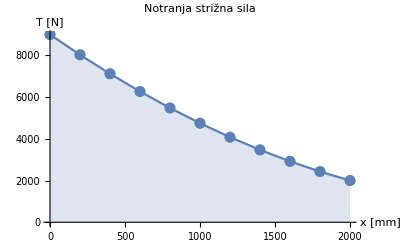

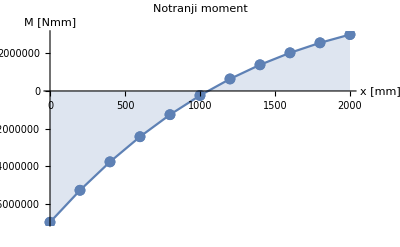

```mathematica
(*Notranja strižna sila in moment*)
Tn=Table[0,{i,1,del+1}];
Mn=Table[0,{i,1,del+1}];
For[i=1,i≤del+1,i++,
Tn[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mn[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]])
]
ListLinePlot[Table[{(i-1)h,Tn[[i]]},{i,1,del+1}],AxesLabel->{"x [mm]","T [N]"},PlotLabel->"Notranja strižna sila", Mesh->Full,Filling->Axis]
ListLinePlot[Table[{(i-1)h,Mn[[i]]},{i,1,del+1}],AxesLabel->{"x [mm]","M [Nmm]"},PlotLabel->"Notranji moment",Mesh->Full,Filling->Axis]
```

## Naloga 2

```mathematica
L=3000.;
M0=1. 10^6;
Ej=200000.;
Iu=171. 10^4;
q0=3.;
qx[x_]=q0 Sin[x/(2L)π];
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==qx[x]/(Ej Iu),
w[0]==0,w''[0]==M0/(Ej Iu),
w[L]==0,w'[L]==0
},w,{x,0,L}];
(*Izris*)
w[x_]=w[x]/.%[[1]];
pwa=Plot[w[x],{x,0,L},PlotLabel->"Upogib analitično",AxesLabel->{"x [mm]","w [mm]"}];
pTa=Plot[-w'''[x]Ej Iu,{x,0,L-3},PlotLabel->"Strig analitično",AxesLabel->{"x [mm]","T [N]"}];
pMa=Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel->"Moment analitično",AxesLabel->{"x [mm]","M [Nmm]"}];
```

### MKR

```mathematica
(*diskretizacija*)
del=20;
h=L/del;
n=del+5;
(*definiramo matriko in vektor*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,3]]=1;
M[[2,{2,3,4}]]={1,-2,1};
b[[2]]=(h^2 M0)/(Ej Iu);
M[[3,-3]]=1;
M[[4,{-4,-2}]]={-1,1};
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=(h^4 qx[(i-1)h])/(Ej Iu);
]
wi=LinearSolve[M,b];
Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]];
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(-0.0204941
-0.0519843
0.
0.117774
0.283652
0.480298
0.69107
0.900362
1.09394
1.25928
1.38585
1.46546
1.49252
1.46433
1.38133
1.24733
1.06974
0.859751
0.63251
0.407273
0.207515
0.0610306
5.42243×10^-18
0.0610306
0.285171)=(0
0.0657895
0
0
0.
0.00034842
0.000694693
0.00103668
0.00137228
0.00169942
0.00201608
0.00232031
0.00261023
0.00288406
0.00314011
0.0033768
0.00359267
0.0037864
0.00395677
0.00410275
0.00422344
0.00431809
0.00438612
0.0044271
0.00444079)

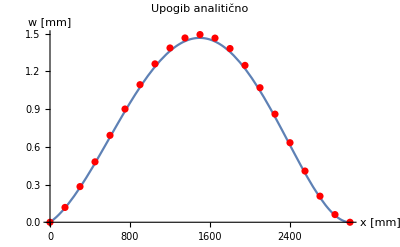

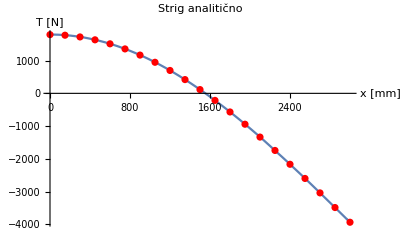

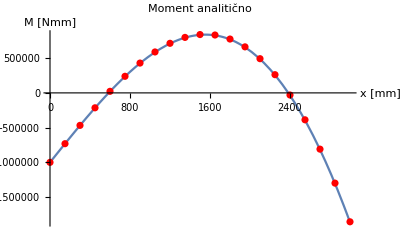

```mathematica
(*izris*)
Ti=Table[0,{i,1,del+1}];
Mi=Table[0,{i,1,del+1}];
For[i=1,i≤del+1,i++,
Ti[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mi[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]])
]
pw=ListPlot[Table[{(i-1)h,wi[[i+2]]},{i,1,n-4}],PlotStyle->Red];
pT=ListPlot[Table[{(i-1)h,Ti[[i]]},{i,1,n-4}],PlotStyle->Red];
pM=ListPlot[Table[{(i-1)h,Mi[[i]]},{i,1,n-4}],PlotStyle->Red];
Show[pwa,pw,PlotRange-> All]
Show[pTa,pT,PlotRange-> All]
Show[pMa,pM,PlotRange-> All]
```

```mathematica
(*reakcije*)
Aza=w'''[0]Ej Iu;
Bza=-w'''[L]Ej Iu;
MBa=-w''[L]Ej Iu;
Print["Analitična rešitev: Az=",Aza," N, Bz=",Bza," N in MB=",MBa," Nmm"]
Az=-Ti[[1]];
Bz=Ti[[-1]];
MB=Mi[[-1]];
Print["MKR rešitev: Az=",Az," N, Bz=",Bz," N in MB=",MB," Nmm"]
```

Analitična rešitev: Az=-1794.67 N, Bz=-3934.9 N in MB=-1.86203×10^6 Nmm

MKR rešitev: Az=-1792.08 N, Bz=-3934.55 N in MB=-1.85533×10^6 Nmm

## Naloga 3

```mathematica
L=3000.;
F0=2. 10^3;
Ej=200000.;
Iu=171. 10^4;
q0=3.;
qx[x_]=q0 Sin[x/(2L)π];
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==qx[x]/(Ej Iu),
w'''[0]==F0/(Ej Iu),w''[0]==0,
w[L]==0,w'[L]==0
},w[x],x];
w[x_]=w[x]/.%[[1]];
pwa=Plot[w[x],{x,0,L},PlotLabel->"Upogib"];
pTa=Plot[-w'''[x]Ej Iu,{x,0,L},PlotLabel->"Strig",Filling->Axis];
pMa=Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel->"Moment",Filling->Axis];
```

### MKR

```mathematica
(*diskr.*)
del=20;
h=L/del;
n=del+5;
(*matrika, vek.*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,{1,2,4,5}]]={-1,2,-2,1};
b[[1]]=(2 h^3 F0)/(Ej Iu);
M[[2,{2,3,4}]]={1,-2,1};
M[[3,-3]]=1;
M[[4,{-4,-2}]]={-1,1};
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=(qx[(i-1)h] h^4)/(Ej Iu);
]
wi=LinearSolve[M,b];

Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]]
```

(-1 | 2 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(98.9062
92.8422
86.7585
80.6748
74.6109
68.5867
62.6232
56.742
50.9665
45.3215
39.8339
34.5329
29.4503
24.621
20.0826
15.8766
12.0476
8.64442
5.71948
3.3295
1.53539
0.402355
1.15433×10^-16
0.402355
1.68789)=(0.0394737
0
0
0
0.
0.00034842
0.000694693
0.00103668
0.00137228
0.00169942
0.00201608
0.00232031
0.00261023
0.00288406
0.00314011
0.0033768
0.00359267
0.0037864
0.00395677
0.00410275
0.00422344
0.00431809
0.00438612
0.0044271
0.00444079)

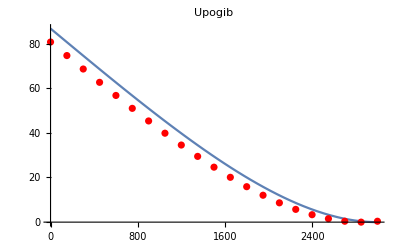

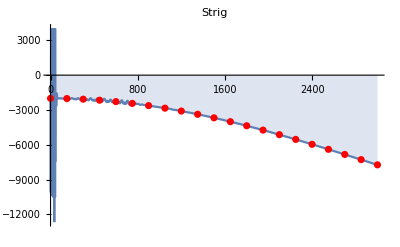

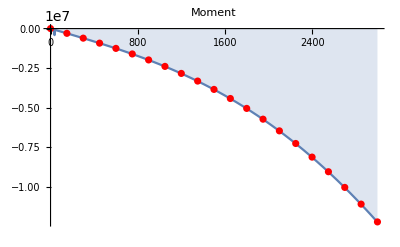

```mathematica
Tn=Table[0,{i,1,del+1}];
Mn=Table[0,{i,1,del+1}];
For[i=1,i≤ del+1,i++,
Tn[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mn[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]]);
]
pw=ListPlot[Table[{(i-1)h,wi[[i+3]]},{i,1,n-4}],PlotStyle->Red];
pT=ListPlot[Table[{(i-1)h,Tn[[i]]},{i,1,n-4}],PlotStyle->Red];
pM=ListPlot[Table[{(i-1)h,Mn[[i]]},{i,1,n-4}],PlotStyle->Red];
Show[pwa,pw,PlotRange-> All]
Show[pTa,pT,PlotRange-> All]
Show[pMa,pM,PlotRange-> All]
```

## Priprave za vajo 13

- obravnava primerov upogiba nosilca po MKE (eno polje in več polj)
- poznavanje (oz. razumevanje) enacbe koncnega elementa upogiba nosilca: 
prostostne stopnje elementa (in pripadajoce sekundarne spremenljivke), 
obravnava porazdeljene obremenitve, 
oblikovne funkcije koncnega elementa.

## Naloga 1

Problem upogiba nosilca obravnavajte po MKE.

```mathematica
(*Podatki*)
L=2 10^3(*mm*);
M0=2 10^6(*N/mm*);
Ej=200000.(*MPa*);
Iu=171. 10^4(*mm^4*);
q0=5.(*N/mm*);
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==q0/(Ej Iu),
w[0]==0,w'[0]==0,
w[L]==0,-w''[L] Ej Iu==-M0
},w[x],x];
w[x_]=w[x]/.%[[1]];
pa=Plot[w[x],{x,0,L}];
```

### MKE

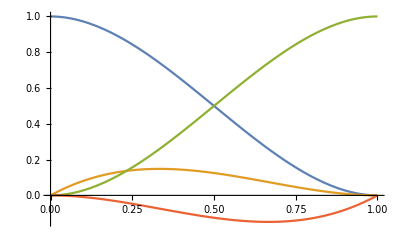

```mathematica
(*diskretizacija*)
ele=4;
h=L/ele;
n=2 ele+2;
(*Končni element*)
Ki[Ee_,Ie_,Le_]=(Ee Ie)/Le^3({{12, 6Le, -12, 6Le}, {6Le, 4 Le^2, -6Le, 2 Le^2}, {-12, -6Le, 12, -6Le}, {6Le, 2 Le^2, -6Le, 4 Le^2}});
ψ1[x_,Le_]=1-3(x/Le)^2+2(x/Le)^3;
ψ2[x_,Le_]=x-2 x^2/Le+x^3/Le^2;
ψ3[x_,Le_]=3 (x/Le)^2-2(x/Le)^3;
ψ4[x_,Le_]=-x^2/Le+x^3/Le^2;
Plot[{ψ1[x,1],ψ2[x,1],ψ3[x,1],ψ4[x,1]},{x,0,1}]
```

```mathematica
(*Definiramo matriko in vektorje*)
Kc=Table[0,{i,1,n},{j,1,n}];
Fi=Fq=Table[0,{i,1,n}];
wi=Table[Subscript[w, i],{i,1,n}];
(*globalna matrika*)
For[i=1,i≤ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu,h];
Fq1=Integrate[q0 ψ1[x,h],{x,0,h}];
Mq1=Integrate[q0 ψ2[x,h],{x,0,h}];
Fq2=Integrate[q0 ψ3[x,h],{x,0,h}];
Mq2=Integrate[q0 ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*Robni pogoji*)
wi[[{1,2,-2}]]=0;
Fi[[1]]=Ra;
Fi[[2]]=Ma;
Fi[[-2]]=Rb;
Fi[[-1]]=M0;
NSolve[Kc.wi==Fi+Fq]
wi=wi/.%[[1]];
povesi=wi[[1;;-1;;2]]
Print[MatrixForm[Kc],MatrixForm[wi],"=",MatrixForm[Fi],MatrixForm[Fq]]
```

{{Ma→-1.5×10^6,Ra→-4750.,Rb→-5250.,w_3→0.296966,w_4→0.000761452,w_5→0.487329,w_6→-0.000121832,w_7→0.205592,w_8→-0.000822368,w_10→0.000487329}}

{0,0.296966,0.487329,0.205592,0}

(32832. | 8.208×10^6 | -32832. | 8.208×10^6 | 0 | 0 | 0 | 0 | 0 | 0
8.208×10^6 | 2.736×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0 | 0 | 0 | 0 | 0
-32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6 | 0 | 0 | 0 | 0
8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0 | 0 | 0
0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6 | 0 | 0
0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0
0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6
0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9
0 | 0 | 0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 32832. | -8.208×10^6
0 | 0 | 0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | -8.208×10^6 | 2.736×10^9)(0
0
0.296966
0.000761452
0.487329
-0.000121832
0.205592
-0.000822368
0
0.000487329)=(Ra
Ma
0
0
0
0
0
0
Rb
2000000)(1250.
104167.
2500.
1.16415×10^-10
2500.
1.16415×10^-10
2500.
1.16415×10^-10
1250.
-104167.)

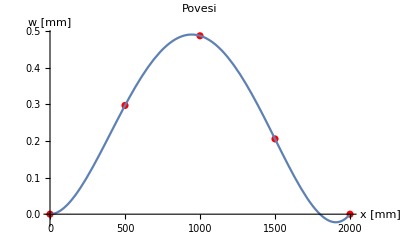

```mathematica
(*Izris upogiba*)
pMKE=ListPlot[Table[{(i-1)h,povesi[[i]]},{i,1,ele+1}],PlotLabel->"Povesi",AxesLabel->{"x [mm]","w [mm]"},PlotStyle->Red];
Show[pMKE,pa,PlotRange-> All]
```

## Naloga 2

```mathematica
(*Podatki*)
L=1 10^3(*mm*);
F0=2 10^3(*N*);
k=5000.(*N/mm*);
Ej=200000.(*MPa*);
{Iu1,Iu2}={342.,171.} 10^4(*mm^4*);
q0=5.(*N/mm*);
qx[x_]=q0-x/(2L) q0;
```

### Analitično

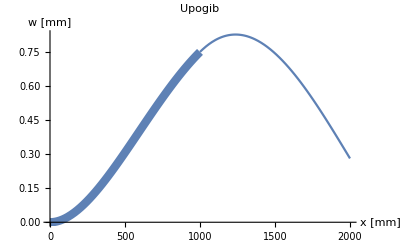

```mathematica
Clear[w1,w2]
NDSolve[{
w1''''[x]==qx[x]/(Ej Iu1),w2''''[x]==qx[x]/(Ej Iu2),
w1[0]==0,w1'[0]==0,-Ej Iu2 w2''[2L]==0,-Ej Iu2 w2'''[2L]==-k w2[2L],
w1[L]==w2[L],w1'[L]==w2'[L],-Ej Iu1 w1''[L]==-Ej Iu2 w2''[L],-Ej Iu1 w1'''[L]==-Ej Iu2 w2'''[L]+F0
},{w1[x],w2[x]},x];
{w1[x_],w2[x_]}={w1[x],w2[x]}/.%[[1]];
p1a=Plot[w1[x],{x,0,L},PlotLabel->"Upogib",AxesLabel->{"x [mm]","w [mm]"},PlotStyle->{Thickness[0.015]}];
p2a=Plot[w2[x],{x,L,2L}];
Show[p1a,p2a,PlotRange->All]
```

### MKE

```mathematica
(*diskretizacija*)
ele=2;
h=L/ele;
n=2 ele+2ele+2;
(*Končni element*)
Ki[Ee_,Ie_,Le_]=(Ee Ie)/Le^3({{12, 6Le, -12, 6Le}, {6Le, 4 Le^2, -6Le, 2 Le^2}, {-12, -6Le, 12, -6Le}, {6Le, 2 Le^2, -6Le, 4 Le^2}});
ψ1[x_,Le_]=1-3(x/Le)^2+2(x/Le)^3;
ψ2[x_,Le_]=x-2 x^2/Le+x^3/Le^2;
ψ3[x_,Le_]=3 (x/Le)^2-2(x/Le)^3;
ψ4[x_,Le_]=-x^2/Le+x^3/Le^2;
(*Matrika in vektorji*)
Kc=Table[0,{i,1,n},{j,1,n}];
Fi=Fq=Table[0,{i,1,n}];
wi=Table[Subscript[w, i],{i,1,n}];
(*Kc1*)
For[i=1,i≤ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu1,h];
x0=(i-1)h;
Fq1=Integrate[qx[x0+x] ψ1[x,h],{x,0,h}];
Mq1=Integrate[qx[x0+x] ψ2[x,h],{x,0,h}];
Fq2=Integrate[qx[x0+x] ψ3[x,h],{x,0,h}];
Mq2=Integrate[qx[x0+x] ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*Kc2*)
For[i=ele+1,i≤ele+ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu2,h];
x0=(i-1)h;
Fq1=Integrate[qx[x0+x] ψ1[x,h],{x,0,h}];
Mq1=Integrate[qx[x0+x] ψ2[x,h],{x,0,h}];
Fq2=Integrate[qx[x0+x] ψ3[x,h],{x,0,h}];
Mq2=Integrate[qx[x0+x] ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*RP*)
wi[[{1,2}]]={0,0};
Fi[[{1,2,-2,-1}]]={Ra,Ma,-k wi[[-2]],0};
(*PKP*)
Fi[[2ele+1]]=F0;
(*Solve*)
NSolve[Kc.wi==Fq+Fi];
wi=wi/.%[[1]];
povesi=wi[[1;;-1;;2]]
Print[MatrixForm[Kc],MatrixForm[wi],"=",MatrixForm[Fi],"+",MatrixForm[Fq]]
```

{0,0.307796,0.751685,0.745403,0.281603}

(65664. | 1.6416×10^7 | -65664. | 1.6416×10^7 | 0 | 0 | 0 | 0 | 0 | 0
1.6416×10^7 | 5.472×10^9 | -1.6416×10^7 | 2.736×10^9 | 0 | 0 | 0 | 0 | 0 | 0
-65664. | -1.6416×10^7 | 131328. | 0. | -65664. | 1.6416×10^7 | 0 | 0 | 0 | 0
1.6416×10^7 | 2.736×10^9 | 0. | 1.0944×10^10 | -1.6416×10^7 | 2.736×10^9 | 0 | 0 | 0 | 0
0 | 0 | -65664. | -1.6416×10^7 | 98496. | -8.208×10^6 | -32832. | 8.208×10^6 | 0 | 0
0 | 0 | 1.6416×10^7 | 2.736×10^9 | -8.208×10^6 | 8.208×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0
0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6
0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9
0 | 0 | 0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 32832. | -8.208×10^6
0 | 0 | 0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | -8.208×10^6 | 2.736×10^9)(0
0
0.307796
0.000960977
0.751685
0.000658589
0.745403
-0.000599744
0.281603
-0.00109533)=(Ra
Ma
0
0
2000
0
0
0
-5000. w_9
0)+(1156.25
93750.
1875.
-20833.3
1250.
-20833.3
625.
-20833.3
93.75
-10416.7)

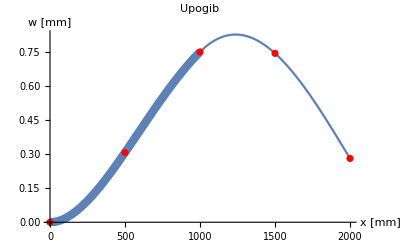

```mathematica
(*izris*)
p=ListPlot[Table[{(i-1)h,povesi[[i]]},{i,1,ele+ele+1}],PlotStyle->Red];
Show[p1a,p2a,p,PlotRange-> All]
```